```mathematica
$MinPrecision=53;
```

### General Parameters

```mathematica
ClearAll[u]
```

```mathematica
Lx=40000;
Ly=20000;
Nx=200;
Ny=100;
uu=0.3;
uuy=0;
uOuterMinPar=3.3;
uOuterMaxPar= 6.6;
ui=10;
uo=10;
```

```mathematica
10^6/1238/24//N
```

33.6564

```mathematica
IDFolderName="/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Lx"<>ToString[Lx]<>"_Ly"<>ToString[Ly]<>"_"<>StringReplace[ToString[uOuterMinPar],"."->"d"]<>"ui"<>ToString[ui]<>"_1uo"<>ToString[uo]<>"_x"<>ToString[Nx]<>"_y"<>ToString[Ny]<>"_ux"<>StringReplace[ToString[uu],"."->"d"]<>"_uy"<>StringReplace[ToString[uuy],"."->"d"]<>"_b"<>ToString[(uOuterMaxPar-uOuterMaxPar/11)//Floor]<>"/Lx"<>ToString[Lx]<>"_Ly"<>ToString[Ly]<>"_"<>StringReplace[ToString[uOuterMinPar],"."->"d"]<>"ui"<>ToString[ui]<>"_1uo"<>ToString[uo]<>"_x"<>ToString[Nx]<>"_y"<>ToString[Ny]<>"_ux"<>StringReplace[ToString[uu],"."->"d"]<>"_uy"<>StringReplace[ToString[uuy],"."->"d"]<>"_b"<>ToString[(uOuterMaxPar-uOuterMaxPar/11)//Floor]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Lx40000_Ly20000_3d3ui10_1uo10_x200_y100_ux0d3_uy0_b6/Lx40000_Ly20000_3d3ui10_1uo10_x200_y100_ux0d3_uy0_b6

### Defining The Domains

#### u Domain(s)

u=1/r

```mathematica
prec=20;
```

```mathematica
uOuterMin=uOuterMinPar;(*The boundary of the inner subdomain*)
uOuterMax= uOuterMaxPar;(*The boundary of the last outer subdomain, should be close to the horizon*)
uOuterDomains=1;(*Number of outer subdomain*)
uOuterNodes=uo;(*Number of points in each outer subdomains*)
uInnerNodes=ui;(*Number of points in the inner subdomains*)
InterfaceNodes=Table[uOuterMin+i(uOuterMax-uOuterMin)/uOuterDomains,{i,0,uOuterDomains,1}];(*This gives the nodes where the subdomains meet*)
```

```mathematica
InterfaceNodes//N
```

{3.3,6.6}

The function below gives an array containing arrays.
Each of these arrays is a subdomain that contains its relative points.

```mathematica
(*GetuDomain[uOutMin_,uOutmax_,uOutDomains_,uOutNodes_,uInnNodes_,IntfaceNodes_]:=Module[{uu=uOutMin},
XInn=Table[-Cos[Pi i/(uInnNodes-1)],{i,0,uInnNodes-1}];
uInner=N[Table[(IntfaceNodes[[1]]+0)/2+(IntfaceNodes[[1]]-0)/2 XInn[[i]],{i,1,uInnNodes}],prec];
XOut=Table[-Cos[Pi i/(uOutNodes-1)],{i,0,uOutNodes-1}];
uOut=N[Flatten[Table[Table[1/2(IntfaceNodes[[j]]+IntfaceNodes[[j-1]])+1/2(IntfaceNodes[[j]]-IntfaceNodes[[j-1]])XOut[[i]],{i,2,uOutNodes}],{j,2,IntfaceNodes//Length}],1],prec];
Join[uInner,uOut]
]*)
```

```mathematica
1/5//N
```

0.2

```mathematica
0.219 2/3
```

0.146

```mathematica
0.219/(6.6/20)
```

0.663636

```mathematica
0.66363 9.9/20
```

0.328497

```mathematica
500/6//N
```

83.3333

```mathematica
GetuDomain2[uOutMin_,uOutmax_,uOutDomains_,uOutNodes_,uInnNodes_,IntfaceNodes_]:=Module[{uu=uOutMin},
XInn=Table[-Cos[Pi i/(uInnNodes-1)],{i,0,uInnNodes-1}];
uInner=N[Table[(IntfaceNodes[[1]]+0)/2+(IntfaceNodes[[1]]-0)/2 XInn[[i]],{i,1,uInnNodes}],prec];
XOut=Table[-Cos[Pi i/(uOutNodes-1)],{i,0,uOutNodes-1}];
uOut=N[Table[Table[1/2(IntfaceNodes[[j]]+IntfaceNodes[[j-1]])+1/2(IntfaceNodes[[j]]-IntfaceNodes[[j-1]])XOut[[i]],{i,1,uOutNodes}],{j,2,IntfaceNodes//Length}],prec];
(*Print[Flatten[uOut,{1}]//Dimensions];*)
Insert[Flatten[uOut,{1}],uInner,1]
]
```

```mathematica
(*uValues=(*{{0.0,0.002025351319275129,0.00793732335844094,0.017256963302735746,0.02922924934990568,0.042884258086335746,0.05711574191366425,0.07077075065009432,0.08274303669726425,0.09206267664155907,0.09797464868072488,0.1},{0.09999999999999998,0.10144367836436871,0.10574782046109107,0.11283224826665475,0.12256499229529424,0.1347647499408149,0.1492042628011086,0.1656145500721956,0.1836899191516714,0.2030936601134971,0.22346431797684174,0.244422425928476,0.265577574071524,0.2865356820231582,0.30690633988650284,0.3263100808483286,0.3443854499278044,0.36079573719889135,0.37523525005918507,0.38743500770470574,0.3971677517333452,0.4042521795389089,0.40855632163563127,0.41000000000000003},{0.41,0.4114436783643687,0.41574782046109104,0.4228322482666548,0.4325649922952942,0.4447647499408149,0.4592042628011086,0.47561455007219555,0.4936899191516714,0.5130936601134971,0.5334643179768417,0.5544224259284759,0.5755775740715239,0.5965356820231582,0.6169063398865028,0.6363100808483285,0.6543854499278043,0.6707957371988913,0.685235250059185,0.6974350077047056,0.7071677517333451,0.7142521795389087,0.7185563216356312,0.72},{0.72,0.7214436783643687,0.7257478204610911,0.7328322482666547,0.7425649922952943,0.7547647499408149,0.7692042628011087,0.7856145500721956,0.8036899191516714,0.8230936601134972,0.8434643179768417,0.864422425928476,0.8855775740715239,0.9065356820231583,0.9269063398865028,0.9463100808483286,0.9643854499278044,0.9807957371988913,0.9952352500591851,1.0074350077047056,1.0171677517333453,1.0242521795389088,1.0285563216356313,1.03}}*)GetuDomain2[uOuterMin,uOuterMax,uOuterDomains,uOuterNodes,uInnerNodes,InterfaceNodes];*)
```

I call the function GetuDomain to define my u-grid.

```mathematica
uValues=GetuDomain2[uOuterMin,uOuterMax,uOuterDomains,uOuterNodes,uInnerNodes,InterfaceNodes];
```

#### x Domain

```mathematica
xMin=-Lx/2;
xMax=Lx/2;
xNodes=Nx;
Deltax=Abs[xMin-xMax]/xNodes;
xValues=Table[xMin+i Deltax,{i,0,xNodes-1}];
```

```mathematica
xValues
```

{-20000,-19800,-19600,-19400,-19200,-19000,-18800,-18600,-18400,-18200,-18000,-17800,-17600,-17400,-17200,-17000,-16800,-16600,-16400,-16200,-16000,-15800,-15600,-15400,-15200,-15000,-14800,-14600,-14400,-14200,-14000,-13800,-13600,-13400,-13200,-13000,-12800,-12600,-12400,-12200,-12000,-11800,-11600,-11400,-11200,-11000,-10800,-10600,-10400,-10200,-10000,-9800,-9600,-9400,-9200,-9000,-8800,-8600,-8400,-8200,-8000,-7800,-7600,-7400,-7200,-7000,-6800,-6600,-6400,-6200,-6000,-5800,-5600,-5400,-5200,-5000,-4800,-4600,-4400,-4200,-4000,-3800,-3600,-3400,-3200,-3000,-2800,-2600,-2400,-2200,-2000,-1800,-1600,-1400,-1200,-1000,-800,-600,-400,-200,0,200,400,600,800,1000,1200,1400,1600,1800,2000,2200,2400,2600,2800,3000,3200,3400,3600,3800,4000,4200,4400,4600,4800,5000,5200,5400,5600,5800,6000,6200,6400,6600,6800,7000,7200,7400,7600,7800,8000,8200,8400,8600,8800,9000,9200,9400,9600,9800,10000,10200,10400,10600,10800,11000,11200,11400,11600,11800,12000,12200,12400,12600,12800,13000,13200,13400,13600,13800,14000,14200,14400,14600,14800,15000,15200,15400,15600,15800,16000,16200,16400,16600,16800,17000,17200,17400,17600,17800,18000,18200,18400,18600,18800,19000,19200,19400,19600,19800}

#### y Domain

```mathematica
yMin = -Ly/2;
yMax = Ly/2;
yNodes = Ny;
Deltay = Abs[yMin - yMax]/yNodes;
yValues = Table[yMin + i Deltay, {i, 0, yNodes - 1}];
```

```mathematica
yMin
```

-10000

#### Grid

Here I define the grid. The first entry is for the number relative to the subdomain,2nd entry is the u-point, 3rd and 4th are for the x and y point. The outpout is the triplet that represent the point in the grid.

```mathematica
MyGrid=Table[{uValues[[i,u]],xValues[[x]],yValues[[y]]},{i,1,uValues//Length},{u,1,uValues[[i]]//Length},{x,1,xValues//Length},{y,1,yValues//Length}];
```

```mathematica
MyGrid[[2,1,1,1]]//Dimensions
```

{3}

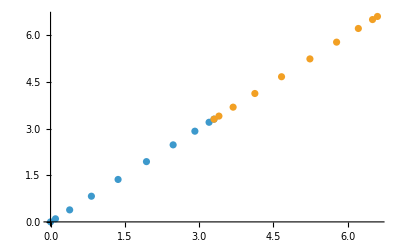

```mathematica
ListPlot[Table[{uValues[[i]],uValues[[i]]}//Transpose,{i,1,uValues//Length}]]
```

## Boosted Black Brane

## Homogeneous boosting

```mathematica
(*gdd=1/ρ^2 Table[ηdd[[u,v]]+,{u,1,4},{v,1,4}]*)
```

Here the goal is to intialise a boosted black brane in an inhomogeneous way, with noise created by a sum of sinusoidal functions each multiplied by small random coefficients

#### Boosting

```mathematica
ClearAll[u1d,u0d,u2d]
u1d[x_,y_]:=uu(*(2 10^5)/(2Pi) 10^-1*);
u2d[x_,y_]:=uuy;
b=(uOuterMax-uOuterMax/11)^-1
```

0.166667

```mathematica
b^3 2//FullForm
```

0.00925926

```mathematica
(*ClearAll[b,u1d]*)
```

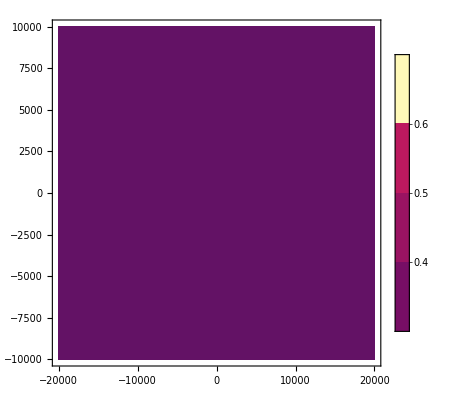

```mathematica
ContourPlot[u1d[x,y],{x,xMin,xMax},{y,yMin,yMax},PlotRange->All,PlotLegends->Automatic(*,ColorFunction->"TemperatureMap"*)(*,MaxRecursion->6*)(*,PlotPoints->20*)]
```

```mathematica
uuy(*ClearAll[b]*)
```

0

```mathematica
90000/(5050/5)//N
60000/(6250/5)//N
```

89.1089

48.

```mathematica
uu
```

0.3

Below I use the definition of u0d.

```mathematica
Solve[u1d[x,y]^2+u2d[x,y]^2-uu0d[x,y]^2==-1,uu0d[x,y]]
```

{{uu0d[x,y]→-1.04403},{uu0d[x,y]→1.04403}}

```mathematica
u0d[x_,y_]:=(*u2d[x,y]/.*)Solve[u1d[x,y]^2+u2d[x,y]^2-uu0d[x,y]^2==-1,uu0d[x,y]][[2,1,2]];
u0d[0,0]
```

1.04403

```mathematica
(*uofρ=NDSolve[{D[u[ρ],ρ]==(u[ρ]^2/ρ^2(1+(b ρ)^3(u1^2+u2^2))^(-1/2)),u[ϵ]==ϵ},u,{ρ,ϵ,1}][[1,1]];*)
```

```mathematica
(*ρofu=DSolve[{D[ρ[u,x,y],{u,1}]==(u^2/ρ[u,x,y]^2(1+(b ρ[u,x,y])^3(u1[x,y]^2+u2[x,y]^2))^(-1/2))^-1},ρ,{u,x,y}][[1,1]];*)
```

Here I compute r in function of rho. I set no boundary conditions for the ODE but I then impose the constant of integration to be zero. 
Note, if too many modes are used for the noise, Mathematica can’t solve this differential equation.

```mathematica
uofρRule=DSolve[{D[u[ρ,x,y],{ρ}]==-u[ρ,x,y]^2(-1/ρ^2(1+(b ρ)^3(u1d[x,y]^2+u2d[x,y]^2))^(-1/2))(*,r[1,x,y]==1*)},u,{ρ,x,y}]//Flatten;
c1Rule=Solve[C[1][x,y]==0(*uofρRule[[1,2]][1,x,y]==1*),C[1][x,y]]//Flatten;
uofρ=u/.uofρRule/.c1Rule//N
```

Function[{ρ,x,y},-(1. ρ)/(0.-1. Hypergeometric2F1[-0.333333,0.5,0.666667,-0.000416667 ρ^3])]

```mathematica
rofρRule=DSolve[{D[r[ρ,x,y],{ρ}]==(-1/ρ^2(1+(b ρ)^3(u1d[x,y]^2+u2d[x,y]^2))^(-1/2))(*,r[1,x,y]==1*)},r,{ρ,x,y}][[1,1]];
rofρ=r/.rofρRule/.c1Rule//N
```

Function[{ρ,x,y},(1. Hypergeometric2F1[-0.333333,0.5,0.666667,-0.000416667 ρ^3])/ρ+0.]

```mathematica
uofρ=Function[{ρ,x,y},(rofρ[ρ,x,y])^-1]
Maximize[uofρ[b^-1,x,y],{x,y(*,xMin,xMax*)}][[1]]//FullForm
```

Function[{ρ,x,y},1/rofρ[ρ,x,y]]

5.8713

!!! The two constant of integration in uofρ and rofρ are not the same !!!

```mathematica
(*c1Rule=Solve[uofρ[1,x,y]==1,C[1][x,y]]//Flatten;*)
```

```mathematica
c1Rule
```

{C[1][x,y]→0}

```mathematica
rofρRule[[2]][b^-1,x,y]/.c1Rule
```

0.17032

```mathematica
Plot3D[uofρRule[[1,2]][b^-1,x,y]/.c1Rule,{y,yMin,yMax},{x,yMin,yMax}]
```

-Graphics3D-

#### a3

Here I compute the initial data for a3. In the limit at infinity, ρ goes to zero, as u. Anyway, they don’t have the same asymptotic behaviour so we need to take the expansion of A, substitute u to its expression that depends on  ρ, and expand in terms of ρ around infinity (where ρ=0). In this way we have an expression of our variable in terms of ρ at infinity that has to match the expression for A in the Turbulence draft (Eq. 3.7).

```mathematica
AExp=1/u^2+u a3[t,u,x,y]+(2 ξ[t,x,y])/u+ξ[t,x,y]^2-2 Derivative[1,0,0][ξ][t,x,y];
```

```mathematica
AExpOfρ=AExp/.u->uofρ[ρ,x,y](*/.c1Rule*)(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,1}]&;
AExpOfρ
```

1/ρ^2+(2. ξ[t,x,y])/ρ+(ξ[t,x,y]^2-2 ξ^(1,0,0)[t,x,y])+(0.000208333+1. a3[t,0,x,y]) ρ+O[ρ]^2

```mathematica
(*AExpOfρ//Normal//Simplify*)
```

```mathematica
AToMatch=ρ^-2(1-(b(*[x,y]*) ρ)^3(1+u1d[x,y]^2+u2d[x,y]^2))//Simplify
```

1/ρ^2-0.0050463 ρ

Let' s look for ξ

```mathematica
xiRule=Solve[Coefficient[AExpOfρ,1/ρ]==Coefficient[AToMatch,1/ρ],  ξ[t,x,y]]//Flatten
```

{ξ[t,x,y]→0.}

```mathematica
(*xiRule=ξ[t,x,y]->-(1.-1. Hypergeometric2F1[-0.3333333333333333,0.5,0.6666666666666666,1. (-0.000811429315297694 Cos[2.7019354914839884+0.05445427266222308 x+0.24294983187761068 y]^2-1. (0.19999999999999998 Cos[5.772098284647657+0.050265482457436686 x+0.12147491593880531 y]+Cos[0.020943951023931956 y])^2)]);*)
```

```mathematica
Solve[SeriesCoefficient[AExpOfρ,{ρ,0,0}]==SeriesCoefficient[AToMatch,{ρ,0,0}]]
```

{{ξ^(1,0,0)[t,x,y]→1/2 ξ[t,x,y]^2}}

I compare the same order coefficient of ρ

```mathematica
a3Rule =Solve[Coefficient[AToMatch,ρ]==Coefficient[AExpOfρ,ρ],a3[t,0,x,y]][[1]]//Simplify
```

{a3[t,0,x,y]→-0.00525463}

```mathematica
11/24 0.5//N
```

0.229167

From Chasler paper a3 should be

```mathematica
Plot[{-1/2 b^3(-1+3 u0d[0.59,y]^2)//Simplify,a3[t,0,x,y]/.a3Rule/.x->0.59},{y,yValues[[1]],yValues[[-1]]}]
```

-Graphics-

Export a3 Initial data

```mathematica
a3Data=Table[(a3[t,0,x,y]/.a3Rule/.x->xValues[[i]]/.y->yValues[[j]])(*+a3Pert[[i,j]]*),{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
xiData=Table[(ξ[t,x,y](*/.ξ[t,x,y]->0*)(*1-Hypergeometric2F1[-0.3333333333333333,0.5,0.6666666666666666,-1/2-1/2 Cos[(2223497 y)/5898008975]]*)/.xiRule/.c1Rule/.x->xValues[[i]]/.y->yValues[[j]])(*(1+(RandomReal[]-0.5)/100)*),{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
(*guessData=Table[N[uofρ[b^-1,x,y]^-1/.c1Rule/.x->xValues[[i]]/.y->yValues[[j]],prec]1,{i,1,xValues//Length},{j,1,yValues//Length}];*)
guessDatarow=Table[N[(uofρRule[[1,2]][b^-1,x,y])^-1/.c1Rule/.x->xValues[[1]]/.y->yValues[[j]],prec]1(*,{i,1,xValues//Length}*),{j,1,yValues//Length}];//AbsoluteTiming
guessData=Table[guessDatarow,xValues//Length];
```

{0.00232,Null}

```mathematica
(uofρRule[[1,2]][b^-1,x,y])^-1/.c1Rule
```

0.17032

```mathematica
a3Data//Length
```

200

```mathematica
a3AttributesAndData={"a3"->a3Data};
```

```mathematica
xiAttributesAndData={"xi"->xiData};
```

```mathematica
guessAttributesAndData={"guess"->guessData};
```

```mathematica
Export[IDFolderName<>"Initiala3_BBB.h5",a3AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Lx40000_Ly20000_3d3ui10_1uo10_x200_y100_ux0d3_uy0_b6/Lx40000_Ly20000_3d3ui10_1uo10_x200_y100_ux0d3_uy0_b6Initiala3_BBB.h5

```mathematica
Export[IDFolderName<>"Initialxi_BBB.h5",xiAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Lx40000_Ly20000_3d3ui10_1uo10_x200_y100_ux0d3_uy0_b6/Lx40000_Ly20000_3d3ui10_1uo10_x200_y100_ux0d3_uy0_b6Initialxi_BBB.h5

```mathematica
Export[IDFolderName<>"Initialguess_BBB.h5",guessAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Lx40000_Ly20000_3d3ui10_1uo10_x200_y100_ux0d3_uy0_b6/Lx40000_Ly20000_3d3ui10_1uo10_x200_y100_ux0d3_uy0_b6Initialguess_BBB.h5

#### f1

Same procedure as above but for F1.

```mathematica
FExp=u f1[t,x,y]+Derivative[0,1,0][ξ][t,x,y]+1/4(-4 f1[t,x,y] ξ[t,x,y](*+3 𝒢^(0,0,1)[t,x,y]*)(*+3 𝒫^(0,1,0)[t,x,y]*))u^2;
```

```mathematica
FExpOfρ=FExp/.u->uofρ[ρ,x,y](*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,2}]&
```

ξ^(0,1,0)[t,x,y]+1. f1[t,x,y] ρ-1. (f1[t,x,y] ξ[t,x,y]) ρ^2+O[ρ]^3

Turbulence draft

```mathematica
(*FToMatch=(b ρ)^3/ρ^2 u0d[x,y] u1d[x,y]*)
```

∂_u Fy=

```mathematica
(*Series[D[rofρ[ρ,x,y],ρ],{ρ,0,3}]*)
```

```mathematica
SeriesCoefficient[FExpOfρ,{ρ,0,1}]
SeriesCoefficient[FToMatch,{ρ,0,1}]
```

1. f1[t,x,y]

-0.000944263

Chasler paper

```mathematica
FToMatch=-(b ρ(*ofu[{0,x,y}]*))^3/(ρ(*ofu[{0,x,y}]*))^2 u0d[x,y] u1d[x,y]
```

-0.00145004 ρ

```mathematica
u0d[x,y]u1d[x,y] b^3
```

0.00145004

```mathematica
(*Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ]*)
```

```mathematica
SeriesCoefficient[FToMatch,{ρ,0,1}]==SeriesCoefficient[FExpOfρ,{ρ,0,1}]
```

-0.00145004==1. f1[t,x,y]

```mathematica
fxRule=Solve[Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ],f1[t,x,y]]//Simplify
```

{{f1[t,x,y]→-0.00145004}}

From Chasler paper this should be.

```mathematica
(*-u0d[x,y] u1d[x,y]*)
```

```mathematica
1500
```

1500

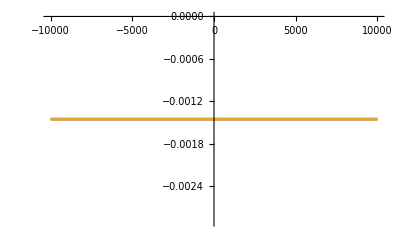

```mathematica
Plot[{- b^3 u0d[1.48,y] u1d[1.48,y],fxRule[[1,1,2]]/.x->1.48},{y,yMin,yMax}]
```

```mathematica
SeriesCoefficient[FToMatch,{ρ,0,0}]
SeriesCoefficient[FExpOfρ,{ρ,0,0}]
```

0

ξ^(0,1,0)[t,x,y]

```mathematica
DSolve[SeriesCoefficient[FToMatch,{ρ,0,0}]==SeriesCoefficient[FExpOfρ,{ρ,0,0}],ξ,{t,x,y}]//Flatten
```

{ξ→Function[{t,x,y},C[1][t,y]]}

```mathematica
DSolve[SeriesCoefficient[FToMatch,{ρ,0,0}]==SeriesCoefficient[FExpOfρ,{ρ,0,2}],ξ,{t,x,y}]//Flatten
```

{ξ→Function[{t,x,y},0.]}

ξ can’t depend on x!

Export fx initial data

```mathematica
(*Maxfx=Maximize[fxRule[[1,1,2]],y][[1]];*)
```

```mathematica
(*fxPertAmpl=5 10^-3;
fxPert=Table[0,{i,1,xValues//Length},{j,1,yValues//Length}];
For [l=2, l≤150,l++,
{AAfx,ϕnfx,nxfx,nyfx}={RandomReal[fxPertAmpl],RandomReal[{0,2π}],RandomInteger[{1,64}],RandomInteger[{1,64}]};
fxPert=Table[fxPert[[i,j]]+AAfx Cos[ϕnfx+(2π)/(xMax-xMin)nxfx xValues[[i]]+(2π)/(xMax-xMin)nyfx yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];];
fxPert=fxPert/Max[fxPert] fxPertAmpl;*)
```

```mathematica
fxData=Table[((f1[t,x,y]/.fxRule[[1]])/.x->xValues[[i]]/.y->yValues[[j]])(*+fxPert[[i,j]]*),{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
Max[fxPert]
```

fxPert

```mathematica
fxData//Dimensions
```

{200,100}

```mathematica
fxAttributesAndData={"fx"->fxData};
```

```mathematica
Export[IDFolderName<>"Initialfx_BBB.h5",fxAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Lx40000_Ly20000_3d3ui10_1uo10_x200_y100_ux0d3_uy0_b6/Lx40000_Ly20000_3d3ui10_1uo10_x200_y100_ux0d3_uy0_b6Initialfx_BBB.h5

#### f2

Same procedure as above but for F1.

```mathematica
F2Exp=u f2[t,z,y]+Derivative[0,0,1][ξ][t,x,y];
```

```mathematica
F2ExpOfρ=F2Exp/.u->uofρ[ρ,x,y]^1(*/.c1Rule*)(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,4}]&;
```

Turbulence draft

```mathematica
(*FToMatch=(b ρ)^3/ρ^2 u0d[x,y] u1d[x,y]*)
```

∂_u Fy=

```mathematica
(*Series[D[rofρ[ρ,x,y],ρ],{ρ,0,3}]*)
```

Chasler paper

```mathematica
F2ToMatch=-(b ρ(*ofu[{0,x,y}]*))^3/(ρ(*ofu[{0,x,y}]*))^2 u0d[x,y] u2d[x,y];
```

```mathematica
(*Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ]*)
```

```mathematica
fyRule=Solve[Coefficient[F2ToMatch,ρ]==Coefficient[F2ExpOfρ,ρ],f2[t,z,y]]//Simplify
```

{{f2[t,z,y]→0.}}

From Chasler paper this should be.

```mathematica
(*-u0d[x,y] u1d[x,y]*)
```

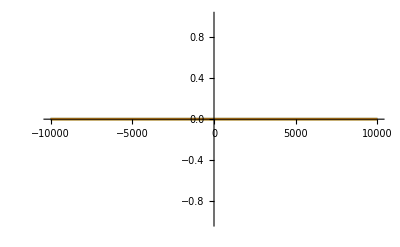

```mathematica
Plot[{-u0d[1.48,y] u2d[1.48,y],fyRule[[1,1,2]]/.x->1.48},{y,yMin,yMax}]
```

```mathematica
DSolve[SeriesCoefficient[F2ToMatch,{ρ,0,0}]==SeriesCoefficient[F2ExpOfρ,{ρ,0,0}],ξ,{t,x,y}]//Flatten
```

{ξ→Function[{t,x,y},C[1][t,x]]}

ξ can’t depend on x!

Export fx initial data

```mathematica
(*fyPertAmpl= 5 10^-3;
fyPert=Table[0,{i,1,xValues//Length},{j,1,yValues//Length}];
For [l=2, l≤100,l++,
{AAfy,ϕnfy,nxfy,nyfy}={RandomReal[fyPertAmpl],RandomReal[{0,2π}],RandomInteger[{1,64}],RandomInteger[{1,64}]};
fyPert=Table[fyPert[[i,j]]+AAfy Cos[ϕnfy+(2π)/(xMax-xMin)nxfy xValues[[i]]+(2π)/(yMax-yMin)nyfy yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];]*)
```

```mathematica
fyPert=fyPert/Max[fyPert] fyPertAmpl;
```

```mathematica
fyData=Table[((f2[t,z,y]/.fyRule[[1]])/.x->xValues[[i]]/.y->yValues[[j]])1(*+fyPert[[i,j]]*),{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
Max[fyData]
```

0.

```mathematica
Norm[fyData]
```

0.

```mathematica
(*fxRule*)
```

```mathematica
fyData//Dimensions
```

{200,100}

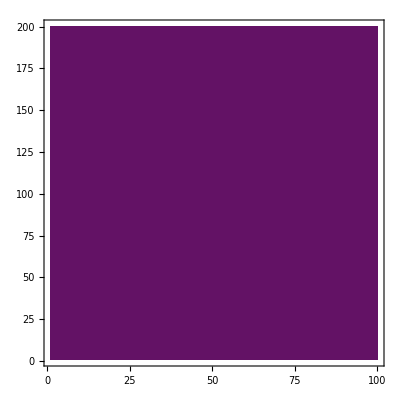

```mathematica
ListContourPlot[fyData]
```

```mathematica
fyAttributesAndData={"fy"->fyData};
```

```mathematica
Export[IDFolderName<>"Initialfy_BBB.h5",fyAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Lx40000_Ly20000_3d3ui10_1uo10_x200_y100_ux0d3_uy0_b6/Lx40000_Ly20000_3d3ui10_1uo10_x200_y100_ux0d3_uy0_b6Initialfy_BBB.h5

```mathematica
(*Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfx_BBB.h5","Data"]*)
```

### B G Functions

#### Grid For ρ

The initial data for B is different, since B is defined through the entire domain. We need to invert the function r(ρ). This is a problem, since that is not invertible analytically.

```mathematica
(*ClearAll[uofρ]*)
```

```mathematica
(*uofρ=Function[{ρs,xs,ys},uofρ/.c1Rule[[1]](*/.ξ->Function[{t,x,y},0]*)/.ρ->ρs/.x->xs/.y->ys]*)
```

```mathematica
(*uofρ[ρs_,xs_,ys_]:=rofρ[[2]]^-1/.c1Rule[[1]]/.ξ->Function[{t,x,y},0]/.ρ->ρs/.x->xs/.y->ys*)
```

```mathematica
(*uofρ=Function[{ρs,xs,ys},uofρ^-1/.c1Rule[[1]]/.ξ->Function[{t,x,y},0]/.ρ->ρs/.x->xs/.y->ys]*)
```

Horizon location

```mathematica
(*rofρ2=r/.DSolve[{D[r[ρ,x,y],{ρ}]==(-1/ρ^2(1+((*b[x,y]*)b ρ)^3(u1d[x,y]^2+u2d[x,y]^2))^(-1/2)),r[1,x,y]==1},r,{ρ,x,y}]//Flatten*)
```

```mathematica
Plot3D[uofρ[b^-1,x,y](*/.b[x,y]->1*)/.c1Rule,{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
uValues[[-1]]
```

{3.3,3.39951,3.68603,4.125,4.66348,5.23652,5.775,6.21397,6.50049,6.6}

```mathematica
Maximize[uofρ[b^-1,x,y],{x,y(*,xMin,xMax*)}][[1]]//FullForm
Minimize[uofρ[b^-1,x,y],{x,y(*,xMin,xMax*)}][[1]]//FullForm
```

5.8713

5.8713

```mathematica
11/20 0.65
```

0.3575

```mathematica
0.35750000000000004/0.219
```

1.63242

```mathematica
(*uofρToInt=ParallelTable[{MyGrid[[i,j,k]],uofρ[MyGrid[[i,j,k]][[1]],MyGrid[[i,j,k]][[2]],MyGrid[[i,j,k]][[3]]]},{i,1,MyGrid//Length},{j,1,MyGrid[[1]]//Length},{k,1,MyGrid[[1,1]]//Length}];//AbsoluteTiming*)
```

```mathematica
(*ρofuOld2=InverseFunction[Function[{ρ,x,y},Intuofρ[ρ,x,y]],1,3];*)
```

```mathematica
ρofuOld=InverseFunction[Function[{ρ,x,y},uofρ[ρ,x,y]],1,3];
```

```mathematica
ρofuOldNumerical[u_?NumericQ,x_,y_]:=ρ/. FindRoot[uofρ[ρ,x,y]==u,{ρ,u},WorkingPrecision->30]//Re;
(*=InverseFunction[Function[{ρ,x,y},uofρ[ρ,x,y]],1,3];*)
```

```mathematica
ClearAll[ρofu,ρofu2]
```

```mathematica
ρofu=Function[C,ρofuOld[C[[1]],C[[2]],C[[3]]]]
```

Function[C,ρofuOld[C⟦1⟧,C⟦2⟧,C⟦3⟧]]

```mathematica
ρofu[{0,1,1}]
```

-8.47033×10^-22

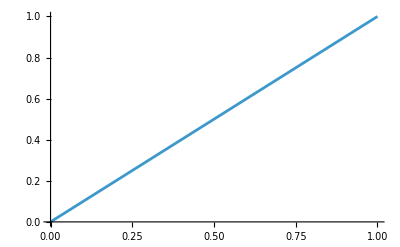

```mathematica
Plot[uofρ[ρ,1,1],{ρ,0,1},PlotRange->All]
```

```mathematica
xRow=Table[ρofu[MyGrid[[n,i,1,k]]],{n,1,uValues//Length},{i,1,uValues[[n]]//Length}(*,{j,1,xValues//Length}*),{k,1,yValues//Length}];//AbsoluteTiming
```

{1.3141,Null}

```mathematica
(*ρofuValues=ParallelTable[ρofu[MyGrid[[n,i,j,k]]],{n,1,uValues//Length},{i,1,uValues[[n]]//Length},{j,1,xValues//Length},{k,1,yValues//Length}];//AbsoluteTiming*)
ρofuValues=Table[xRow[[n,i,k]],{n,1,uValues//Length},{i,1,uValues[[n]]//Length},{j,1,xValues//Length},{k,1,yValues//Length}];//AbsoluteTiming
```

{0.164506,Null}

```mathematica
u1Values=Table[u1d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.026286,Null}

```mathematica
u2Values=Table[u2d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.022577,Null}

```mathematica
u0Values=Table[u0d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{14.3834,Null}

#### B Function

```mathematica
ClearAll[InitialBAnalytic]
```

```mathematica
InitialBAnalytic[u_,x_,y_]:=-1/2 Log[(1+(b ρofu[{u,x,y}])^3 u1d[x,y]^2)/(1+(b ρofu[{u,x,y}])^3 u2d[x,y]^2)] u^-3;
```

```mathematica
InitialB1row=Table[N[SeriesCoefficient[InitialBAnalytic[u,xValues[[1]],yValues[[j]]],{u,uValues[[1,1]],0}]//Normal](*(1+10^-4( RandomReal[]-0.5))*),{j,1,yNodes}];//AbsoluteTiming
InitialB1=Table[InitialB1row,{i,1,xValues//Length}];//AbsoluteTiming
```

{28.5284,Null}

{0.000016,Null}

```mathematica
(*InitialB1=ParallelTable[N[SeriesCoefficient[InitialBAnalytic[u,xValues[[i]],yValues[[j]]],{u,uValues[[1,1]],0}]//Normal](*(1+10^-4( RandomReal[]-0.5))*),{i,1,xNodes},{j,1,yNodes}];//AbsoluteTiming*)
```

```mathematica
InitialB1[[2,5]]
```

-0.000208333

```mathematica
(*InitialB=ParallelTable[N[-1/2Log[(1+(b ρofuValues[[n,ui,xi,yi]])^3 u1Values[[xi,yi]]^2)/(1+(b ρofuValues[[n,ui,xi,yi]])^3 u2Values[[xi,yi]]^2)] uValues[[n,ui]]^-3,$MinPrecision](*(1+(RandomReal[]-0.5)/10^4)*),{n,1,uValues//Length},{ui,1,uValues[[n]]//Length},{xi,1,xNodes},{yi,1,yNodes}];//AbsoluteTiming
InitialB[[1,1]]=InitialB1(*Table[-0.5,{i,1,25},{j,1,25}]*);
(*InitialB[[1]]=InitialB[[2]];*)*)
InitialBrow=Table[N[-1/2 Log[(1+(b ρofuValues[[n,ui,1,yi]])^3 u1Values[[1,yi]]^2)/(1+(b ρofuValues[[n,ui,1,yi]])^3 u2Values[[1,yi]]^2)] uValues[[n,ui]]^-3,$MinPrecision](*(1+(RandomReal[]-0.5)/10^4)*),{n,1,uValues//Length},{ui,1,uValues[[n]]//Length}(*,{xi,1,xNodes}*),{yi,1,yNodes}];//AbsoluteTiming
InitialB=Table[InitialBrow[[n,i,k]],{n,1,uValues//Length},{i,1,uValues[[n]]//Length},{j,1,xValues//Length},{k,1,yValues//Length}];(*Transpose[Table[InitialBrow,{i,1,xValues//Length}],3]//Transpose[#,{1,2,4,3}]&;*)
InitialB[[1,1]]=InitialB1;
```

Power::infy: Infinite expression 1/0.^3 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^3 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^3 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{0.021753,Null}

```mathematica
InitialB[[-1,1,1,1]]
```

-0.000209118

```mathematica
ExportAttributes=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndData=Table[ExportAttributes[[i]]->(InitialB[[i]]//Re),{i,1,ExportAttributes//Length}];//AbsoluteTiming
```

{0.084695,Null}

```mathematica
Export[IDFolderName<>"InitialB_BBB.h5",AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Lx40000_Ly20000_3d3ui10_1uo10_x200_y100_ux0d3_uy0_b6/Lx40000_Ly20000_3d3ui10_1uo10_x200_y100_ux0d3_uy0_b6InitialB_BBB.h5

#### G Function

```mathematica
ArcSinh[(b^3 u1 u2 ρ^3)/(√(1+b^3 (u1^2+u2^2) ρ^3))]//TrigToExp//Together//Simplify
```

Log[(0.00462963 u1 u2 ρ^3)/(√(1+0.00462963 (u1^2+u2^2) ρ^3))+√(1+(0.0000214335 u1^2 u2^2 ρ^6)/(1+0.00462963 (u1^2+u2^2) ρ^3))]

```mathematica
(*InitialG=ParallelTable[N[ArcSinh[(b^3 u1Values[[xi,yi]] u2Values[[xi,yi]] ρofuValues[[n,ui,xi,yi]]^3)/(√(1+b^3 (u1Values[[xi,yi]]^2+u2Values[[xi,yi]]^2) ρofuValues[[n,ui,xi,yi]]^3))](*Log[(b^3 u1Values[[n,ui]] u2Values[[xi,yi]] ρofuValues[[n,ui,xi,yi]]^3+√((1+b^3 uValues[[n,ui]]^2 ρofuValues[[n,ui,xi,yi]]^3) (1+b^3 u2Values[[xi,yi]]^2 ρofuValues[[n,ui,xi,yi]]^3)))/(√(1+b^3 (uValues[[n,ui]]^2+u2Values[[xi,yi]]^2) ρofuValues[[n,ui,xi,yi]]^3))]*)uValues[[n,ui]]^-3,$MinPrecision](*+((RandomReal[]-0.5)/10^4)*),{n,1,uValues//Length},{ui,1,uValues[[n]]//Length},{xi,1,xNodes},{yi,1,yNodes}];//AbsoluteTiming*)
InitialGrow=Table[N[ArcSinh[(b^3 u1Values[[1,yi]] u2Values[[1,yi]] ρofuValues[[n,ui,1,yi]]^3)/(√(1+b^3 (u1Values[[1,yi]]^2+u2Values[[1,yi]]^2) ρofuValues[[n,ui,1,yi]]^3))](*Log[(b^3 u1Values[[n,ui]] u2Values[[xi,yi]] ρofuValues[[n,ui,xi,yi]]^3+√((1+b^3 uValues[[n,ui]]^2 ρofuValues[[n,ui,xi,yi]]^3) (1+b^3 u2Values[[xi,yi]]^2 ρofuValues[[n,ui,xi,yi]]^3)))/(√(1+b^3 (uValues[[n,ui]]^2+u2Values[[xi,yi]]^2) ρofuValues[[n,ui,xi,yi]]^3))]*)uValues[[n,ui]]^-3,$MinPrecision](*+((RandomReal[]-0.5)/10^4)*),{n,1,uValues//Length},{ui,1,uValues[[n]]//Length},(*{xi,1,xNodes},*){yi,1,yNodes}]//Quiet;//AbsoluteTiming
InitialG=Table[InitialGrow[[n,i,k]],{n,1,uValues//Length},{i,1,uValues[[n]]//Length},{j,1,xValues//Length},{k,1,yValues//Length}];(*Transpose[Table[InitialGrow,{i,1,xValues//Length}],3]//Transpose[#,{1,2,4,3}]&;*)
```

{0.017753,Null}

```mathematica
InitialGAnalytic[u_,x_,y_]:=ArcSinh[(b^3 u1d[x,y] u2d[x,y] ρofu[{u,x,y}]^3)/(√(1+b^3 (u1d[x,y]^2+u2d[x,y]^2) ρofu[{u,x,y}]^3))](*Log[(b^3 u1d[x,y] u2d[x,y] ρofu[{u,x,y}]^3+√((1+b^3 u1d[x,y]^2 ρofu[{u,x,y}]^3) (1+b^3 u2d[x,y]^2 ρofu[{u,x,y}]^3)))/(√(1+b^3 (u1d[x,y]^2+u2d[x,y]^2) ρofu[{u,x,y}]^3))]*)u^-3;
```

```mathematica
(*InitialG1=ParallelTable[N[SeriesCoefficient[InitialGAnalytic[u,xValues[[i]],yValues[[j]]],{u,uValues[[1,1]],0}]//Normal],{i,1,xNodes},{j,1,yNodes}];//AbsoluteTiming*)
InitialG1row=Table[N[SeriesCoefficient[InitialGAnalytic[u,xValues[[1]],yValues[[j]]],{u,uValues[[1,1]],0}]//Normal](*+( (RandomReal[]-0.5)/10^4)*)(*,{i,1,xNodes}*),{j,1,yNodes}];//AbsoluteTiming
InitialG1=Table[InitialG1row,{i,1,xValues//Length}];
InitialG[[1,1]]=InitialG1;
```

{0.005954,Null}

```mathematica
InitialG//Dimensions
```

{2,10,200,100}

```mathematica
InitialG[[1,5,;;,;;]]//ListPlot3D
```

-Graphics3D-

```mathematica
ExportAttributesG=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndDataG=Table[ExportAttributesG[[i]]->(InitialG[[i]]//Re),{i,1,ExportAttributesG//Length}];//AbsoluteTiming
```

{0.0913,Null}

```mathematica
Export[IDFolderName<>"InitialG_BBB.h5",AttributesAndDataG,"Datasets"];
```

## Source Function

#### Tanh Source

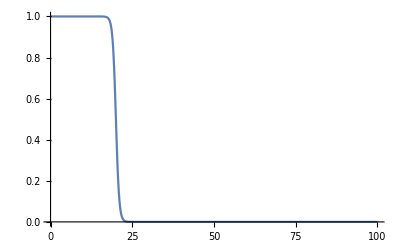

```mathematica
Plot[1-A(1/2(1+Tanh[t-t0]))/.A->1/.t0->20,{t,0,100},PlotRange->All]
```

```mathematica
1-1/2(1+Tanh[(t-t0)/tau])A  /.A->0.1/.t0->100/.tau->20/.t->0//FullForm
1-1/2(1+Tanh[(t-t0)/tau])A  /.A->0.1/.t0->20/.tau->1/.t->0//FullForm
```

0.999995

1.

```mathematica
1/150 1/((sigmax )^2 2Pi)/.sigmax->1/64//N
```

4.34599

```mathematica
S0[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_]:=1-1/2(1+Tanh[(t-t0)/tau])A  1/((sigmax )^2 2Pi)Exp[(-( x -x0)^2)/(2 (L sigmax )^2)] 1/((sigmay )^2 2Pi)Exp[(-(y -y0)^2)/(2 (L sigmay )^2)];
```

```mathematica
S0tilt[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_,phi_]:=1-1/2 (1+Tanh[(t-t0)/tau])*A*Exp[-1/2*((((x-x0) Cos[phi]+(y-y0) Sin[phi])^2)/(L sigmax)^2+((-(x-x0) Sin[phi]+(y-y0) Cos[phi])^2)/(L sigmay)^2)]//FullSimplify;
```

```mathematica
Series[1-A Exp[(-( x )^2)/(2 (L sigmax )^2)],{x,0,2}]
```

(1-A)+(A x^2)/(2 L^2 sigmax^2)+O[x]^3

```mathematica
1/(1Pi(0.125^2))0.006//N
```

0.122231

```mathematica
D[S0[t,20,1,0.006,0,0,0.25,0,0,0.25]/.L->500,t]/.t->20
D[S0[t,5000,300,0.006,0,0,0.25,0,0,0.25]/.L->500,t]/.t->5000
D[S0[t,5000,5000,0.006,0,0,0.25,0,0,0.25]/.L->500,t]/.t->5000
S0[t,5000,5000,0.006,0,0,0.25,0,0,0.25]/.L->500/.t->0//FullForm
(*D[S0[t,10000,6000,0.006,0,0,0.25,0,0,0.25]/.L->500,t]/.t->10000
D[S0[t,20000,12000,0.006,0,0,0.25,0,0,0.25]/.L->500,t]/.t->20000*)
```

-0.003

-0.00001

-6.×10^-7

0.999285

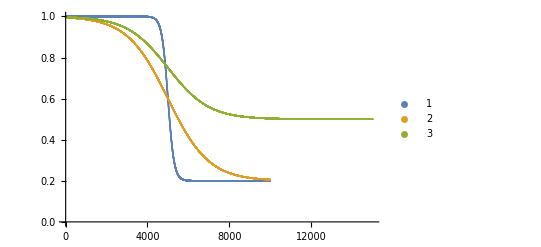

```mathematica
ListPlot[{Table[{t,S0[t,5000,300,0.8,0,0,0.25,0,0,0.25]/.L->500}(*,{x,-100000,100000}*),{t,0,10000}],Table[{t,S0[t,5000,2000,0.8,0,0,0.25,0,0,0.25]/.L->500}(*,{x,-100000,100000}*),{t,0,10000}],Table[{t,S0[t,5000,2000,0.5,0,0,0.25,0,0,0.25]/.L->500}(*,{x,-100000,100000}*),{t,0,15000}]},PlotRange->All,PlotLegends->Automatic]
```

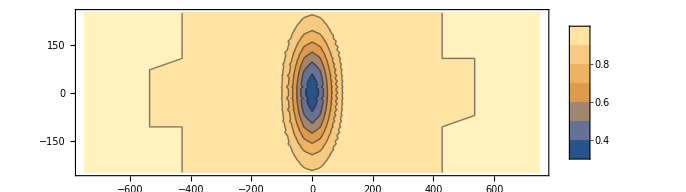

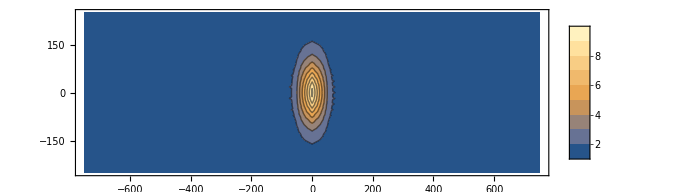

-Graphics-

```mathematica
t0test=5000;
tautest=2000;
Atest=0.675;
sigmaxtest= 1/10 500;
sigmaytest=1/4 500;
x0test=0;
y0test=0;

ContourPlot[{S0[10000,t0test,tautest,Atest,x,x0test,sigmaxtest,y,y0test,sigmaytest]/.L->1},{x,-750,750},{y,-250,250},PlotRange->All,PlotLegends->Automatic,ImageSize->Large,AspectRatio->1/3]
ContourPlot[{S0[10000,t0test,tautest,Atest,x,x0test,sigmaxtest,y,y0test,sigmaytest]^-2/.L->1},{x,-750,750},{y,-250,250},PlotRange->All,PlotLegends->Automatic,ImageSize->Large,AspectRatio->1/3]
ContourPlot[S0tilt[10000,t0test,tautest,Atest,x,x0test,sigmaxtest,y,y0test,sigmaytest,0.9]/.L->1/.L->1,{x,-750,750},{y,-250,250},PlotRange->All,PlotLegends->Automatic,ImageSize->Large,AspectRatio->1/3]
```

```mathematica
Plot3D[{D[S0[10000,t0test,tautest,Atest,xx,x0test,sigmaxtest,y,y0test,sigmaytest]/.L->1,{xx,2}]/.xx->x},{x,-750,750},{y,-250,250},PlotRange->All,PlotLegends->Automatic,ImageSize->Large,AspectRatio->1/3]
```

-Graphics3D-

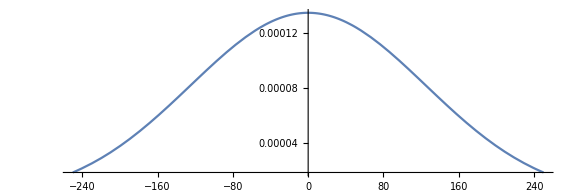

```mathematica
Plot[D[S0[5000,t0test,tautest,Atest,xx,x0test,sigmaxtest,y,y0test,sigmaytest]/.L->1,{xx,1}]/.xx->1,{y,-250,250},PlotRange->All,PlotLegends->Automatic,ImageSize->Large,AspectRatio->1/3]
```

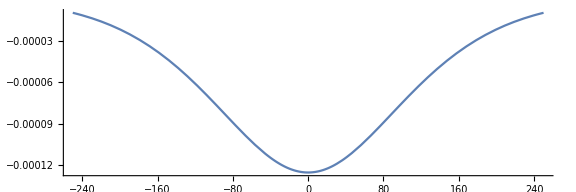

```mathematica
Plot[D[S0[5000,t0test,tautest,Atest,xx,x0test,sigmaxtest,y,y0test,sigmaytest]^(-1/2)/.L->1,{xx,1}]/.xx->1,{y,-250,250},PlotRange->All,PlotLegends->Automatic,ImageSize->Large,AspectRatio->1/3]
```

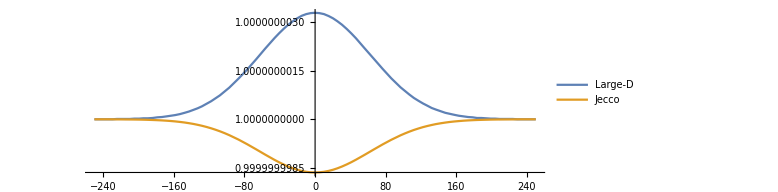

```mathematica
Plot[{S0[10000,t0test,tautest,1,x,x0test,1/8 500,y,y0test,1/8 500]^-2/.L->1/.x->0,S0[10000,t0test,tautest,1,x,x0test,1/8 500,y,y0test,1/8 500]/.L->1/.x->0},{y,-250,250},PlotRange->All,PlotLegends->{"Large-D","Jecco"},ImageSize->Large,AspectRatio->1/3]
```

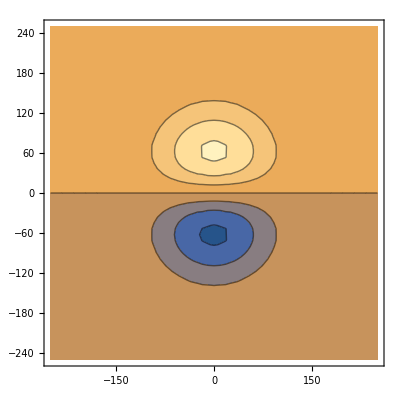

```mathematica
ContourPlot[D[S0[10000,t0test,tautest,1,x,x0test,1/8 500,yy,y0test,1/8 500],yy]/.L->1/.x->0/.yy->y,{x,-250,250},{y,-250,250},PlotRange->All]
```

```mathematica
D[S0[10000,t0test,tautest,1,x,x0test,1/8 500,yy,y0test,1/8 500],yy]
```

(8 ⅇ^(-(2 x^2)/(15625 L^2)-(2 yy^2)/(15625 L^2)) yy (1+Tanh[5/2]))/(3814697265625 L^2 π^2)

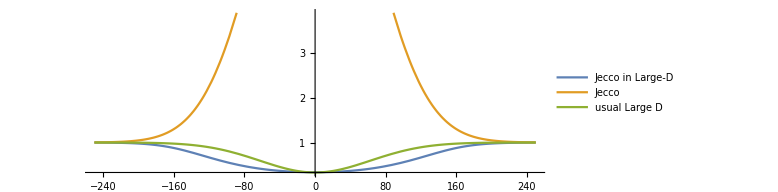

```mathematica
Plot[{S0[10000,t0test,tautest,Atest,x,x0test,sigmaxtest,y,y0test,sigmaytest]^(-1/2)/.L->1/.x->0,S0[10000,t0test,tautest,Atest,x,x0test,sigmaxtest,y,y0test,sigmaytest]/.L->1/.x->0,S0[10000,t0test,tautest,0.675,x,x0test,1/8 500,y,y0test,1/8 500]/.L->1/.x->0},{y,-250,250},(*PlotRange->All,*)PlotLegends->{"Jecco in Large-D","Jecco","usual Large D"},ImageSize->Large,AspectRatio->1/3]
```

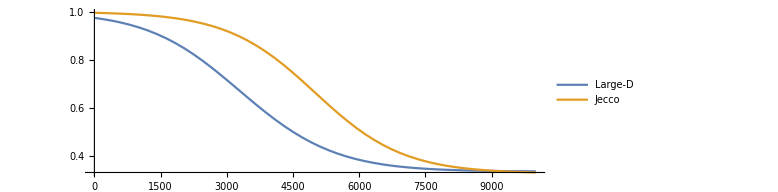

```mathematica
Plot[{D[S0[tt,t0test,tautest,-8,0,x0test,1/10 500,0,y0test,1/10 500]^(-1/2)/.L->1/.x->0,{tt,0}]/.tt->{t},D[S0[tt,t0test,tautest,Atest,0,x0test,sigmaxtest,0,y0test,sigmaytest]/.L->1/.x->0,{tt,0}]/.tt->{t}},{t,0,10000},PlotRange->All,PlotLegends->{"Large-D","Jecco"},ImageSize->Large,AspectRatio->1/3]
```

```mathematica
rules={A->GS[Amp],L->GS[L],Lx->GS[Lx],Ly->GS[Ly],x0->GS[x0],y0->GS[y0],sigmax->GS[sigmax],sigmay->GS[sigmay],t0->GS[t0],tau->GS[tau],phi->GS[phi]}
```

{A→GS[Amp],L→GS[L],Lx→GS[Lx],Ly→GS[Ly],x0→GS[x0],y0→GS[y0],sigmax→GS[sigmax],sigmay→GS[sigmay],t0→GS[t0],tau→GS[tau],phi→GS[phi]}

```mathematica
expr=S0[t,t0,tau,A,x,x0,sigmax,y,y0,sigmay(*,{x,1},{y,1}*),phi]//FullSimplify;//AbsoluteTiming
```

$Aborted

```mathematica
newExpr=expr/. rules//Simplify//FortranForm;
(*First,replace GS(...) safely*)expr1=StringReplace[ToString[newExpr],"GS("~~(param:(LetterCharacter|DigitCharacter)..)~~")":>"GS."<>param];
(*Then,process exponentiation and other fixes separately*)
expr2=StringReplace[expr1,{"E**"->"MathConstants.e^"}];
expr3=StringReplace[expr2,{"**"->"^"}];
expr4=StringReplace[expr3,{"**"->"^",(*Fix power notation after GS replacement*)"e"~~(x:DigitCharacter..):>"e"<>x,(*Fix scientific notation*)x:(DigitCharacter..)~~"."~~(y:Except[DigitCharacter]..):>x<>y,(*Remove unnecessary dots*)"Pi"->"pi",(*Mathematica uses'Pi',Julia uses'pi'*)"Tanh"->"tanh","Cos"->"cos","Sin"->"sin"}];
```

```mathematica
expr3//Print
```

1 - (GS.Amp*(1 + Tanh((t - GS.t0)/GS.tau)))/(2.*MathConstants.e^(((x - GS.x0)^2/GS.sigmax^2 + (y - GS.y0)^2/GS.sigmay^2)/(2.*L^2)))

```mathematica
SetOptions[$Output,PageWidth->Infinity];

(*Define the function Sz*)
Sz[t_,x_,y_]:=S0[t,t0,tau,A,x,x0,sigmax,y,y0,sigmay,phi]; (*Replace'expr' with the actual function*)

(*Compute derivatives*)
Szx[t_,x_,y_]=D[Sz[t,x,y],x];
Szxx[t_,x_,y_]=D[Szx[t,x,y],x];
Szxxx[t_,x_,y_]=D[Szxx[t,x,y],x];
Szxxxx[t_,x_,y_]=D[Szxxx[t,x,y],x];

Szy[t_,x_,y_]=D[Sz[t,x,y],y];
Szxy[t_,x_,y_]=D[Szx[t,x,y],y];
Szxxy[t_,x_,y_]=D[Szxx[t,x,y],y];
Szxyy[t_,x_,y_]=D[Szxy[t,x,y],y];
Szxxyy[t_,x_,y_]=D[Szxxy[t,x,y],y];

Szyy[t_,x_,y_]=D[Szy[t,x,y],y];
Szyyy[t_,x_,y_]=D[Szyy[t,x,y],y];
Szyyyy[t_,x_,y_]=D[Szyyy[t,x,y],y];

Szt[t_,x_,y_]=D[Sz[t,x,y],t];
Sztt[t_,x_,y_]=D[Szt[t,x,y],t];
Sztx[t_,x_,y_]=D[Szt[t,x,y],x];
Szty[t_,x_,y_]=D[Szt[t,x,y],y];
Sztxx[t_,x_,y_]=D[Sztx[t,x,y],x];
Sztyy[t_,x_,y_]=D[Szty[t,x,y],y];
Sztxy[t_,x_,y_]=D[Sztx[t,x,y],y];


(*Function to process expressions*)
processExpression[expr_]:=Module[{newExpr,expr1,expr2,expr3,expr4},newExpr=expr/. rules//Simplify//FortranForm;
expr1=StringReplace[ToString[newExpr],"GS("~~(param:(LetterCharacter|DigitCharacter)..)~~")":>"GS."<>param];
expr2=StringReplace[expr1,{"E**"->"exp"}];
expr3=StringReplace[expr2,{"**"->"^"}];
expr4=StringReplace[expr3,{"Pi"->"pi"}];
expr5=StringReplace[expr4,{"**"->"^","e"~~(x:DigitCharacter..):>"e"<>x,x:(DigitCharacter..)~~"."~~(y:Except[DigitCharacter]..):>x<>y,"Pi"->"pi","Tanh"->"tanh","Sech"->"sech","Sqrt"->"sqrt","Sinh"->"sinh","Cosh"->"cosh","Cos"->"cos","Sin"->"sin"}];
expr5];
SourceType="GaussianTilt";
(*Process all expressions*)
expressions={"Sz(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sz[t,x,y]],"Sz_x(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szx[t,x,y]],"Sz_xx(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxx[t,x,y]],"Sz_xxx(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxxx[t,x,y]],"Sz_xxxx(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxxxx[t,x,y]],"Sz_y(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szy[t,x,y]],"Sz_xy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxy[t,x,y]],"Sz_xxy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxxy[t,x,y]],"Sz_xyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxyy[t,x,y]],"Sz_xxyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxxyy[t,x,y]],"Sz_yy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szyy[t,x,y]],"Sz_yyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szyyy[t,x,y]],"Sz_yyyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szyyyy[t,x,y]],"Sz_t(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szt[t,x,y]],"Sz_tt(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztt[t,x,y]],"Sz_tx(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztx[t,x,y]],"Sz_ty(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szty[t,x,y]],"Sz_txx(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztxx[t,x,y]],"Sz_tyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztyy[t,x,y]],"Sz_txy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztxy[t,x,y]]};

(*Export to file*)
Export["/home/giulio/University/PhD/translated_expressions.txt",expressions,"Text"];
```

```mathematica
expressions[[6]]
```

Sz_y(t, x, y, GS ::PertSource) = (GS.Amp*(y - GS.y0)*(1 + tanh((t - GS.t0)/GS.tau)))/(2*exp(((x - GS.x0)^2/GS.sigmax^2 + (y - GS.y0)^2/GS.sigmay^2)/(2*L^2))*L^2*GS.sigmay^2)

```mathematica
Sz[t,x,y]
```

1-1/2 A ⅇ^(-(x-x0)^2/(2 L^2 sigmax^2)-(y-y0)^2/(2 L^2 sigmay^2)) (1+Tanh[(t-t0)/tau])

```mathematica
D[S0[t,t0,tau,A,x,x0,sigmax,y,y0,sigmay],y]
```

(A ⅇ^(-(x-x0)^2/(2 L^2 sigmax^2)-(y-y0)^2/(2 L^2 sigmay^2)) (y-y0) (1+Tanh[(t-t0)/tau]))/(2 L^2 sigmay^2)

#### Perturbative Source

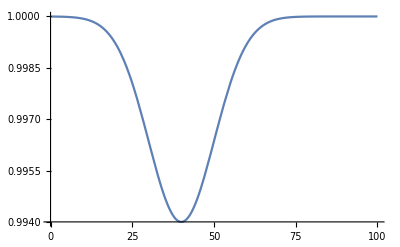

```mathematica
Plot[1-A Exp[(-( t -t0)^2)/(2  tau^2)]/.A->0.006/.t0->40/.tau->10,{t,0,100},PlotRange->All]
```

```mathematica
S0[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_]:=1-Exp[(-( t -t0)^2)/(2  tau^2)]A  (*1/((sigmax )^2 2Pi)*)Exp[(-( x -x0)^2)/(2 (L sigmax )^2)](*1/((sigmay )^2 2Pi)*)Exp[(-(y -y0)^2)/(2 (L sigmay )^2)];
```

```mathematica
1/(1Pi(0.125^2))0.006//N
```

0.122231

```mathematica
S0[20,100,20,0.006,0,0,0.25,0,0,0.25]/.L->500
S0[20,20,1,0.006,0,0,0.25,0,0,0.25]/.L->500
```

0.999998

0.994

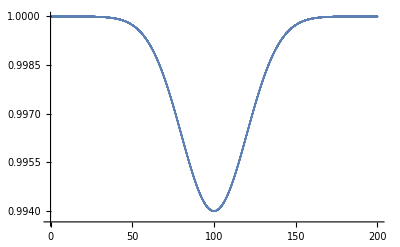

```mathematica
ListPlot[Table[{t,S0[t,100,20,0.006,0,0,0.25,0,0,0.25]/.L->500}(*,{x,-100000,100000}*),{t,0,200,0.013}],PlotRange->All,PlotLegends->Automatic]
```

```mathematica
rules={A->GS[Amp],L->GS[L],x0->GS[x0],y0->GS[y0],sigmax->GS[sigmax],sigmay->GS[sigmay],t0->GS[t0],tau->GS[tau]}
```

{A→GS[Amp],L→GS[L],x0→GS[x0],y0→GS[y0],sigmax→GS[sigmax],sigmay→GS[sigmay],t0→GS[t0],tau→GS[tau]}

```mathematica
SetOptions[$Output,PageWidth->Infinity];

(*Define the function Sz*)
Sz[t_,x_,y_]:=S0[t,t0,tau,A,x,x0,sigmax,y,y0,sigmay]; (*Replace'expr' with your actual function*)

(*Compute derivatives*)
Szx[t_,x_,y_]=D[Sz[t,x,y],x];
Szxx[t_,x_,y_]=D[Szx[t,x,y],x];
Szxxx[t_,x_,y_]=D[Szxx[t,x,y],x];
Szxxxx[t_,x_,y_]=D[Szxxx[t,x,y],x];

Szy[t_,x_,y_]=D[Sz[t,x,y],y];
Szxy[t_,x_,y_]=D[Szx[t,x,y],y];
Szxxy[t_,x_,y_]=D[Szxx[t,x,y],y];
Szxyy[t_,x_,y_]=D[Szxy[t,x,y],y];
Szxxyy[t_,x_,y_]=D[Szxxy[t,x,y],y];

Szyy[t_,x_,y_]=D[Szy[t,x,y],y];
Szyyy[t_,x_,y_]=D[Szyy[t,x,y],y];
Szyyyy[t_,x_,y_]=D[Szyyy[t,x,y],y];

Szt[t_,x_,y_]=D[Sz[t,x,y],t];
Sztt[t_,x_,y_]=D[Szt[t,x,y],t];
Sztx[t_,x_,y_]=D[Szt[t,x,y],x];
Szty[t_,x_,y_]=D[Szt[t,x,y],y];
Sztxx[t_,x_,y_]=D[Sztx[t,x,y],x];
Sztyy[t_,x_,y_]=D[Szty[t,x,y],y];
Sztxy[t_,x_,y_]=D[Sztx[t,x,y],y];


(*Function to process expressions*)
processExpression[expr_]:=Module[{newExpr,expr1,expr2,expr3,expr4},newExpr=expr/. rules//Simplify//FortranForm;
expr1=StringReplace[ToString[newExpr],"GS("~~(param:(LetterCharacter|DigitCharacter)..)~~")":>"GS."<>param];
expr2=StringReplace[expr1,{"E**"->"MathConstants.e^"}];
expr3=StringReplace[expr2,{"**"->"^"}];
expr4=StringReplace[expr3,{"Pi"->"pi"}];
expr5=StringReplace[expr4,{"**"->"^","e"~~(x:DigitCharacter..):>"e"<>x,x:(DigitCharacter..)~~"."~~(y:Except[DigitCharacter]..):>x<>y,"Pi"->"pi","Tanh"->"tanh","Sech"->"sech","Sqrt"->"sqrt","Sinh"->"sinh","Cosh"->"cosh"}];
expr5];
SourceType="PertSource";
(*Process all expressions*)
expressions={"Sz(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sz[t,x,y]],"Sz_x(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szx[t,x,y]],"Sz_xx(t, x, y, GS ::"<>SourceType<>") ="<>processExpression[Szxx[t,x,y]],"Sz_xxx(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxxx[t,x,y]],"Sz_xxxx(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxxxx[t,x,y]],"Sz_y(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szy[t,x,y]],"Sz_xy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxy[t,x,y]],"Sz_xxy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxxy[t,x,y]],"Sz_xyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxyy[t,x,y]],"Sz_xxyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxxyy[t,x,y]],"Sz_yy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szyy[t,x,y]],"Sz_yyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szyyy[t,x,y]],"Sz_yyyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szyyyy[t,x,y]],"Sz_t(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szt[t,x,y]],"Sz_tt(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztt[t,x,y]],"Sz_tx(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztx[t,x,y]],"Sz_ty(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szty[t,x,y]],"Sz_txx(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztxx[t,x,y]],"Sz_tyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztyy[t,x,y]],"Sz_txy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztxy[t,x,y]]};

(*Export to file*)
Export["/home/giulio/University/PhD/translated_expressions.txt",expressions,"Text"];
```

#### Exponential Source

```mathematica
ClearAll[L]
```

```mathematica
S0Exp[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_]:=(1+1/(1+E^((-(t-t0))/tau))A  1/((sigmax )^2 2Pi)Exp[(-(( x -x0)(2Pi)/L)^2)/(2 (sigmax )^2)] 1/((sigmay )^2 2Pi)Exp[(-(( y (2Pi)/L-y0)(2Pi)/L)^2)/(2 (sigmay )^2)])^(-1/2);
```

```mathematica
(-(( x -x0)(2Pi)/L)^2)/(2 (sigmax )^2)//Expand
```

-(2 π^2 x^2)/(L^2 sigmax^2)+(4 π^2 x x0)/(L^2 sigmax^2)-(2 π^2 x0^2)/(L^2 sigmax^2)

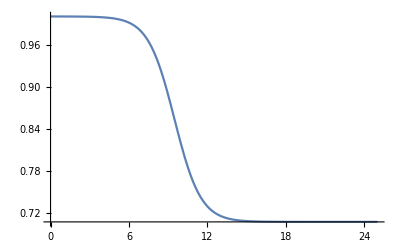

```mathematica
Plot[(1+1/(1+E^((-(t-t0))/tau)))^(-1/2)/.tau->1/.t0->10,{t,0,25},PlotRange->All]
```

```mathematica
rules={A->GS[Amp],L->GS[L],x0->GS[x0],y0->GS[y0],sigmax->GS[sigmax],sigmay->GS[sigmay],t0->GS[t0],tau->GS[tau]}
```

{A→GS[Amp],L→GS[L],x0→GS[x0],y0→GS[y0],sigmax→GS[sigmax],sigmay→GS[sigmay],t0→GS[t0],tau→GS[tau]}

```mathematica
expr=S0Exp[t,t0,tau,A,x,x0,sigmax,y,y0,sigmay(*,{x,1},{y,1}*)]//FullSimplify
```

1/(√(1+(A ⅇ^((2 π^2 (-(x-x0)^2/sigmax^2-(-2 π y+L y0)^2/(L^2 sigmay^2)))/L^2))/(4 (1+ⅇ^((-t+t0)/tau)) π^2 sigmax^2 sigmay^2)))

```mathematica
D[S0[t,0,1,0.01,x,0,1,y,0,1(*,{x,1},{y,1}*)],{t,1}]/.t->0/.x->-0(*/.y->-100000*)/.L->200000
```

0.

```mathematica
newExpr=expr/. rules//Simplify//FortranForm;
(*First,replace GS(...) safely*)expr1=StringReplace[ToString[newExpr],"GS("~~(param:(LetterCharacter|DigitCharacter)..)~~")":>"GS."<>param];
(*Then,process exponentiation and other fixes separately*)
expr2=StringReplace[expr1,{"E**"->"MathConstants.e^"}];
expr3=StringReplace[expr2,{"**"->"^"}];
expr4=StringReplace[expr3,{"**"->"^",(*Fix power notation after GS replacement*)"e"~~(x:DigitCharacter..):>"e"<>x,(*Fix scientific notation*)x:(DigitCharacter..)~~"."~~(y:Except[DigitCharacter]..):>x<>y,(*Remove unnecessary dots*)"Pi"->"pi",(*Mathematica uses'Pi',Julia uses'pi'*)"Tanh"->"tanh"}];
```

```mathematica
expr3//Print
```

1/Sqrt(1 + (MathConstants.e^((2*Pi^2*(-((x - GS.x0)^2/GS.sigmax^2) - (-2*Pi*y + GS.L*GS.y0)^2/(GS.L^2*GS.sigmay^2)))/GS.L^2)*GS.Amp)/(4.*(1 + MathConstants.e^((-t + GS.t0)/GS.tau))*Pi^2*GS.sigmax^2*GS.sigmay^2))

```mathematica
SetOptions[$Output,PageWidth->Infinity];

(*Define the function Sz*)
Sz[t_,x_,y_]:=S0[t,t0,tau,A,x,x0,sigmax,y,y0,sigmay]; (*Replace'expr' with your actual function*)

(*Compute derivatives*)
Szx[t_,x_,y_]=D[Sz[t,x,y],x];
Szxx[t_,x_,y_]=D[Szx[t,x,y],x];
Szxxx[t_,x_,y_]=D[Szxx[t,x,y],x];
Szxxxx[t_,x_,y_]=D[Szxxx[t,x,y],x];

Szy[t_,x_,y_]=D[Sz[t,x,y],y];
Szxy[t_,x_,y_]=D[Szx[t,x,y],y];
Szxxy[t_,x_,y_]=D[Szxx[t,x,y],y];
Szxyy[t_,x_,y_]=D[Szxy[t,x,y],y];
Szxxyy[t_,x_,y_]=D[Szxxy[t,x,y],y];

Szyy[t_,x_,y_]=D[Szy[t,x,y],y];
Szyyy[t_,x_,y_]=D[Szyy[t,x,y],y];
Szyyyy[t_,x_,y_]=D[Szyyy[t,x,y],y];

Szt[t_,x_,y_]=D[Sz[t,x,y],t];
Sztt[t_,x_,y_]=D[Szt[t,x,y],t];
Sztx[t_,x_,y_]=D[Szt[t,x,y],x];
Szty[t_,x_,y_]=D[Szt[t,x,y],y];
Sztxx[t_,x_,y_]=D[Sztx[t,x,y],x];
Sztyy[t_,x_,y_]=D[Szty[t,x,y],y];
Sztxy[t_,x_,y_]=D[Sztx[t,x,y],y];


(*Function to process expressions*)
processExpression[expr_]:=Module[{newExpr,expr1,expr2,expr3,expr4},newExpr=expr/. rules//Simplify//FortranForm;
expr1=StringReplace[ToString[newExpr],"GS("~~(param:(LetterCharacter|DigitCharacter)..)~~")":>"GS."<>param];
expr2=StringReplace[expr1,{"E**"->"MathConstants.e^"}];
expr3=StringReplace[expr2,{"**"->"^"}];
expr4=StringReplace[expr3,{"Pi"->"pi"}];
expr5=StringReplace[expr4,{"**"->"^","e"~~(x:DigitCharacter..):>"e"<>x,x:(DigitCharacter..)~~"."~~(y:Except[DigitCharacter]..):>x<>y,"Pi"->"pi","Tanh"->"tanh","Sech"->"sech","Sqrt"->"sqrt","Sinh"->"sinh","Cosh"->"cosh"}];
expr5];

(*Process all expressions*)
expressions={"Sz(t, x, y, GS ::ExpSource) = "<>processExpression[Sz[t,x,y]],"Sz_x(t, x, y, GS ::ExpSource) = "<>processExpression[Szx[t,x,y]],"Sz_xx(t, x, y, GS ::ExpSource) = "<>processExpression[Szxx[t,x,y]],"Sz_xxx(t, x, y, GS ::ExpSource) = "<>processExpression[Szxxx[t,x,y]],"Sz_xxxx(t, x, y, GS ::ExpSource) = "<>processExpression[Szxxxx[t,x,y]],"Sz_y(t, x, y, GS ::ExpSource) = "<>processExpression[Szy[t,x,y]],"Sz_xy(t, x, y, GS ::ExpSource) = "<>processExpression[Szxy[t,x,y]],"Sz_xxy(t, x, y, GS ::ExpSource) = "<>processExpression[Szxxy[t,x,y]],"Sz_xyy(t, x, y, GS ::ExpSource) = "<>processExpression[Szxyy[t,x,y]],"Sz_xxyy(t, x, y, GS ::ExpSource) = "<>processExpression[Szxxyy[t,x,y]],"Sz_yy(t, x, y, GS ::ExpSource) = "<>processExpression[Szyy[t,x,y]],"Sz_yyy(t, x, y, GS ::ExpSource) = "<>processExpression[Szyyy[t,x,y]],"Sz_yyyy(t, x, y, GS ::ExpSource) = "<>processExpression[Szyyyy[t,x,y]],"Sz_t(t, x, y, GS ::ExpSource) = "<>processExpression[Szt[t,x,y]],
"Sz_tt(t, x, y, GS ::ExpSource) = "<>processExpression[Sztt[t,x,y]],"Sz_tx(t, x, y, GS ::ExpSource) = "<>processExpression[Sztx[t,x,y]],"Sz_ty(t, x, y, GS ::ExpSource) = "<>processExpression[Szty[t,x,y]],"Sz_txx(t, x, y, GS ::ExpSource) = "<>processExpression[Sztxx[t,x,y]],"Sz_tyy(t, x, y, GS ::ExpSource) = "<>processExpression[Sztyy[t,x,y]],"Sz_txy(t, x, y, GS ::ExpSource) = "<>processExpression[Sztxy[t,x,y]]};

(*Export to file*)
Export["/home/giulio/University/PhD/translated_expressions.txt",expressions,"Text"];
```

#### Constant Source

```mathematica
S0Const[t_,t0_,tau_,A_]:=(1+(1+Tanh[(t-t0)/tau])A  )^(-1/2);
```

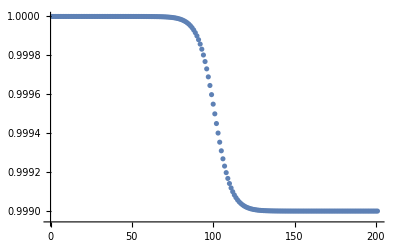

```mathematica
ListPlot[Table[S0Const[t,10,1,0.001]/.L->20^5(*,{x,-100000,100000}*),{t,0,20,0.1}],PlotRange->All,PlotLegends->Automatic]
```

```mathematica
rules={A->GS[Amp],L->GS[L],x0->GS[x0],y0->GS[y0],sigmax->GS[sigmax],sigmay->GS[sigmay],t0->GS[t0],tau->GS[tau]}
```

{A→GS[Amp],L→GS[L],x0→GS[x0],y0→GS[y0],sigmax→GS[sigmax],sigmay→GS[sigmay],t0→GS[t0],tau→GS[tau]}

```mathematica
expr=S0Const[t,t0,tau,A]//FullSimplify
```

1/(√(1+A+A Tanh[(t-t0)/tau]))

```mathematica
newExpr=expr/. rules//Simplify//FortranForm;
(*First,replace GS(...) safely*)expr1=StringReplace[ToString[newExpr],"GS("~~(param:(LetterCharacter|DigitCharacter)..)~~")":>"GS."<>param];
(*Then,process exponentiation and other fixes separately*)
expr2=StringReplace[expr1,{"E**"->"MathConstants.e^"}];
expr3=StringReplace[expr2,{"**"->"^"}];
expr4=StringReplace[expr3,{"**"->"^",(*Fix power notation after GS replacement*)"e"~~(x:DigitCharacter..):>"e"<>x,(*Fix scientific notation*)x:(DigitCharacter..)~~"."~~(y:Except[DigitCharacter]..):>x<>y,(*Remove unnecessary dots*)"Pi"->"pi",(*Mathematica uses'Pi',Julia uses'pi'*)"Tanh"->"tanh"}];
```

```mathematica
expr3//Print
```

1/Sqrt(1 + GS.Amp*(1 + Tanh((t - GS.t0)/GS.tau)))

```mathematica
SetOptions[$Output,PageWidth->Infinity];

(*Define the function Sz*)
Sz[t_,x_,y_]:=S0Const[t,t0,tau,A]; (*Replace'expr' with your actual function*)

(*Compute derivatives*)
Szx[t_,x_,y_]=D[Sz[t,x,y],x];
Szxx[t_,x_,y_]=D[Szx[t,x,y],x];
Szxxx[t_,x_,y_]=D[Szxx[t,x,y],x];
Szxxxx[t_,x_,y_]=D[Szxxx[t,x,y],x];

Szy[t_,x_,y_]=D[Sz[t,x,y],y];
Szxy[t_,x_,y_]=D[Szx[t,x,y],y];
Szxxy[t_,x_,y_]=D[Szxx[t,x,y],y];
Szxyy[t_,x_,y_]=D[Szxy[t,x,y],y];
Szxxyy[t_,x_,y_]=D[Szxxy[t,x,y],y];

Szyy[t_,x_,y_]=D[Szy[t,x,y],y];
Szyyy[t_,x_,y_]=D[Szyy[t,x,y],y];
Szyyyy[t_,x_,y_]=D[Szyyy[t,x,y],y];

Szt[t_,x_,y_]=D[Sz[t,x,y],t];
Sztt[t_,x_,y_]=D[Szt[t,x,y],t];
Sztx[t_,x_,y_]=D[Szt[t,x,y],x];
Szty[t_,x_,y_]=D[Szt[t,x,y],y];
Sztxx[t_,x_,y_]=D[Sztx[t,x,y],x];
Sztyy[t_,x_,y_]=D[Szty[t,x,y],y];
Sztxy[t_,x_,y_]=D[Sztx[t,x,y],y];


(*Function to process expressions*)
processExpression[expr_]:=Module[{newExpr,expr1,expr2,expr3,expr4},newExpr=expr/. rules//Simplify//FortranForm;
expr1=StringReplace[ToString[newExpr],"GS("~~(param:(LetterCharacter|DigitCharacter)..)~~")":>"GS."<>param];
expr2=StringReplace[expr1,{"E**"->"MathConstants.e^"}];
expr3=StringReplace[expr2,{"**"->"^"}];
expr4=StringReplace[expr3,{"Pi"->"pi"}];
expr5=StringReplace[expr4,{"**"->"^","e"~~(x:DigitCharacter..):>"e"<>x,x:(DigitCharacter..)~~"."~~(y:Except[DigitCharacter]..):>x<>y,"Pi"->"pi","Tanh"->"tanh","Sech"->"sech","Sqrt"->"sqrt","Sinh"->"sinh","Cosh"->"cosh"}];
expr5];

(*Process all expressions*)
expressions={"Sz(t, x, y, GS ::SpatialConstantSource) = "<>processExpression[Sz[t,x,y]],"Sz_x(t, x, y, GS ::SpatialConstantSource) = "<>processExpression[Szx[t,x,y]],"Sz_xx(t, x, y, GS ::SpatialConstantSource) = "<>processExpression[Szxx[t,x,y]],"Sz_xxx(t, x, y, GS ::SpatialConstantSource) = "<>processExpression[Szxxx[t,x,y]],"Sz_xxxx(t, x, y, GS ::SpatialConstantSource) = "<>processExpression[Szxxxx[t,x,y]],"Sz_y(t, x, y, GS ::SpatialConstantSource) = "<>processExpression[Szy[t,x,y]],"Sz_xy(t, x, y, GS ::SpatialConstantSource) = "<>processExpression[Szxy[t,x,y]],"Sz_xxy(t, x, y, GS ::SpatialConstantSource) = "<>processExpression[Szxxy[t,x,y]],"Sz_xyy(t, x, y, GS ::SpatialConstantSource) = "<>processExpression[Szxyy[t,x,y]],"Sz_xxyy(t, x, y, GS ::SpatialConstantSource) = "<>processExpression[Szxxyy[t,x,y]],"Sz_yy(t, x, y, GS ::SpatialConstantSource) = "<>processExpression[Szyy[t,x,y]],"Sz_yyy(t, x, y, GS ::SpatialConstantSource) = "<>processExpression[Szyyy[t,x,y]],"Sz_yyyy(t, x, y, GS ::SpatialConstantSource) = "<>processExpression[Szyyyy[t,x,y]],"Sz_t(t, x, y, GS ::SpatialConstantSource) = "<>processExpression[Szt[t,x,y]],"Sz_tt(t, x, y, GS ::SpatialConstantSource) = "<>processExpression[Sztt[t,x,y]],"Sz_tx(t, x, y, GS ::SpatialConstantSource) = "<>processExpression[Sztx[t,x,y]],"Sz_ty(t, x, y, GS ::SpatialConstantSource) = "<>processExpression[Szty[t,x,y]],"Sz_txx(t, x, y, GS ::SpatialConstantSource) = "<>processExpression[Sztxx[t,x,y]],"Sz_tyy(t, x, y, GS ::SpatialConstantSource) = "<>processExpression[Sztyy[t,x,y]],"Sz_txy(t, x, y, GS ::SpatialConstantSource) = "<>processExpression[Sztxy[t,x,y]]};

(*Export to file*)
Export["/home/giulio/University/PhD/translated_expressions.txt",expressions,"Text"];
```

```mathematica
Sz[t,x,y]
```

1/(√(1+A (1+Tanh[(t-t0)/tau])))

```mathematica
processExpression[D[Sz[t,x,y],x,y]]
```

0

#### Transported Gaussian Source

```mathematica
1-1-1/2(1+Tanh[t-t0])/.tau->1/.t0->20/.t->0//N[#,16]&
```

-4.248354255291589×10^-18

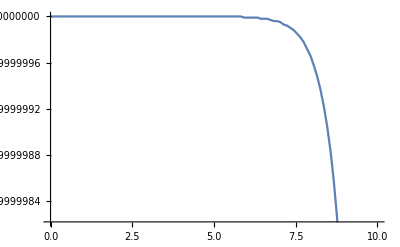

```mathematica
Plot[{(1-1/2(1+Tanh[(t-t0)/tau]))/.tau->1/.t0->20(*,1-(1+Tanh[t-t0])/.t0->5*)},{t,0,10}]
```

```mathematica
S0transp[t_,t0_,tau_,v_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_]:=(1-(1/2(1+Tanh[(t-t0)/tau])A  1/(sigmax )Exp[(-(x+v t -x0)^2)/(2 (sigmax )^2)] 1/((sigmay ) (2Pi))Exp[(-( y -y0)^2)/(2 (sigmay )^2)]))^(-1/2)//Simplify;
```

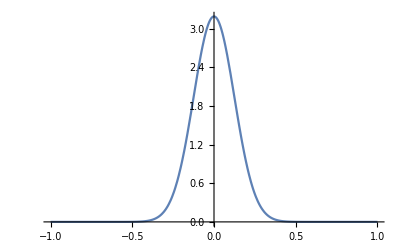

```mathematica
Plot[A 1/((2Pi)^(1/2)sigmax) Exp[-1/2((x -x0)/(sigmax ))^2]/.A->1/.sigmax-> 0.125/.x0->0/.L->2,{x,-1,1},PlotRange->All]
```

```mathematica
rules={A->GS[Amp],L->GS[L],x0->GS[x0],y0->GS[y0],sigmax->GS[sigmax],sigmay->GS[sigmay],t0->GS[t0],tau->GS[tau],v->GS[v]}
```

{A→GS[Amp],L→GS[L],x0→GS[x0],y0→GS[y0],sigmax→GS[sigmax],sigmay→GS[sigmay],t0→GS[t0],tau→GS[tau],v→GS[v]}

```mathematica
expr=S0transp[t,t0,tau,v,A,x,x0,sigmax,y,y0,sigmay(*,{x,1},{y,1}*)]//FullSimplify
```

1/(√(1-(A ⅇ^(-(t v+x-x0)^2/(2 sigmax^2)-(y-y0)^2/(2 sigmay^2)) (1+Tanh[(t-t0)/tau]))/(4 π sigmax sigmay)))

```mathematica
1/(√(1-(A ⅇ^(-(t v+x-x0)^2/(2 sigmax^2)-(y-y0)^2/(2 sigmay^2)) (1+Tanh[(t-t0)/tau]))/(4 π sigmax sigmay)))
```

1/(√(1-(A ⅇ^(-(t v+x-x0)^2/(2 sigmax^2)-(y-y0)^2/(2 sigmay^2)) (1+Tanh[(t-t0)/tau]))/(4 π sigmax sigmay)))

```mathematica
1-(A ⅇ^(-(x-x0)^2/(2 sigmax^2)-(y-y0)^2/(2 sigmay^2)) (1+Tanh[(t-t0)/tau]))/(4 π sigmax sigmay)
```

1-(A ⅇ^(-(x-x0)^2/(2 sigmax^2)-(y-y0)^2/(2 sigmay^2)) (1+Tanh[(t-t0)/tau]))/(4 π sigmax sigmay)

s(t,x,y)=1-(A ⅇ^(-(x-x0)^2/(2 σ_x^2)-(y-y0)^2/(2 σ_y^2)) (1+Tanh[(t-t0)/tau]))/(4 π σ_x σ_y)

```mathematica
Plot[]
```

Plot::argrx: «4» called with «1» arguments; «1» arguments are expected.

Plot[]

```mathematica
newExpr=expr/. rules//Simplify//FortranForm;
(*First,replace GS(...) safely*)expr1=StringReplace[ToString[newExpr],"GS("~~(param:(LetterCharacter|DigitCharacter)..)~~")":>"GS."<>param];
(*Then,process exponentiation and other fixes separately*)
expr2=StringReplace[expr1,{"E**"->"MathConstants.e^"}];
expr3=StringReplace[expr2,{"**"->"^"}];
expr4=StringReplace[expr3,{"**"->"^",(*Fix power notation after GS replacement*)"e"~~(x:DigitCharacter..):>"e"<>x,(*Fix scientific notation*)x:(DigitCharacter..)~~"."~~(y:Except[DigitCharacter]..):>x<>y,(*Remove unnecessary dots*)"Pi"->"pi",(*Mathematica uses'Pi',Julia uses'pi'*)"Tanh"->"tanh"}];
```

```mathematica
expr3//Print
```

1/Sqrt(1 - (MathConstants.e^(-0.5*(x + t*GS.v - GS.x0)^2/GS.sigmax^2 - (y - GS.y0)^2/(2.*GS.sigmay^2))*GS.Amp*(1 + Tanh((t - GS.t0)/GS.tau)))/(4.*Pi*GS.sigmax*GS.sigmay))

```mathematica
SetOptions[$Output,PageWidth->Infinity];

(*Define the function Sz*)
Sz[t_,x_,y_]:=S0transp[t,t0,tau,v,A,x,x0,sigmax,y,y0,sigmay]; (*Replace'expr' with your actual function*)

(*Compute derivatives*)
Szx[t_,x_,y_]=D[Sz[t,x,y],x];
Szxx[t_,x_,y_]=D[Szx[t,x,y],x];
Szxxx[t_,x_,y_]=D[Szxx[t,x,y],x];
Szxxxx[t_,x_,y_]=D[Szxxx[t,x,y],x];

Szy[t_,x_,y_]=D[Sz[t,x,y],y];
Szxy[t_,x_,y_]=D[Szx[t,x,y],y];
Szxxy[t_,x_,y_]=D[Szxx[t,x,y],y];
Szxyy[t_,x_,y_]=D[Szxy[t,x,y],y];
Szxxyy[t_,x_,y_]=D[Szxxy[t,x,y],y];

Szyy[t_,x_,y_]=D[Szy[t,x,y],y];
Szyyy[t_,x_,y_]=D[Szyy[t,x,y],y];
Szyyyy[t_,x_,y_]=D[Szyyy[t,x,y],y];

Szt[t_,x_,y_]=D[Sz[t,x,y],t];
Sztt[t_,x_,y_]=D[Szt[t,x,y],t];
Sztx[t_,x_,y_]=D[Szt[t,x,y],x];
Szty[t_,x_,y_]=D[Szt[t,x,y],y];
Sztxx[t_,x_,y_]=D[Sztx[t,x,y],x];
Sztyy[t_,x_,y_]=D[Szty[t,x,y],y];
Sztxy[t_,x_,y_]=D[Sztx[t,x,y],y];


(*Function to process expressions*)
processExpression[expr_]:=Module[{newExpr,expr1,expr2,expr3,expr4},newExpr=expr/. rules//Simplify//FortranForm;
expr1=StringReplace[ToString[newExpr],"GS("~~(param:(LetterCharacter|DigitCharacter)..)~~")":>"GS."<>param];
expr2=StringReplace[expr1,{"E**"->"MathConstants.e^"}];
expr3=StringReplace[expr2,{"**"->"^"}];
expr4=StringReplace[expr3,{"Pi"->"pi"}];
expr5=StringReplace[expr4,{"**"->"^","e"~~(x:DigitCharacter..):>"e"<>x,x:(DigitCharacter..)~~"."~~(y:Except[DigitCharacter]..):>x<>y,"Pi"->"pi","Tanh"->"tanh","Sech"->"sech","Sqrt"->"sqrt","Sinh"->"sinh","Cosh"->"cosh"}];
expr5];
SourceType="MovingGaussianSource";
(*Process all expressions*)
expressions={"Sz(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sz[t,x,y]],"Sz_x(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szx[t,x,y]],"Sz_xx(t, x, y, GS ::"<>SourceType<>") ="<>processExpression[Szxx[t,x,y]],"Sz_xxx(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxxx[t,x,y]],"Sz_xxxx(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxxxx[t,x,y]],"Sz_y(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szy[t,x,y]],"Sz_xy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxy[t,x,y]],"Sz_xxy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxxy[t,x,y]],"Sz_xyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxyy[t,x,y]],"Sz_xxyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxxyy[t,x,y]],"Sz_yy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szyy[t,x,y]],"Sz_yyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szyyy[t,x,y]],"Sz_yyyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szyyyy[t,x,y]],"Sz_t(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szt[t,x,y]],"Sz_tt(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztt[t,x,y]],"Sz_tx(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztx[t,x,y]],"Sz_ty(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szty[t,x,y]],"Sz_txx(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztxx[t,x,y]],"Sz_tyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztyy[t,x,y]],"Sz_txy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztxy[t,x,y]]};

(*Export to file*)
Export["/home/giulio/University/PhD/translated_expressions.txt",expressions,"Text"];
```

```mathematica
Sz[t,x,y]
```

1/(√(1-(A ⅇ^(-(t v+x-x0)^2/(2 sigmax^2)-(y-y0)^2/(2 sigmay^2)) (1+Tanh[(t-t0)/tau]))/(4 π sigmax sigmay)))

```mathematica
processExpression[D[Sz[t,x,y],x,y]]
```

(sqrt(pi)*GS.Amp*(x + t*GS.v - GS.x0)*(y - GS.y0)*(1 + tanh((t - GS.t0)/GS.tau))*(8*MathConstants.e^(((x + t*GS.v - GS.x0)^2/GS.sigmax^2 + (y - GS.y0)^2/GS.sigmay^2)/2)*pi*GS.sigmax*GS.sigmay + GS.Amp*(1 + tanh((t - GS.t0)/GS.tau))))/(2*GS.sigmax^2*GS.sigmay^2*sqrt((MathConstants.e^(-0.5*(x + t*GS.v - GS.x0)^2/GS.sigmax^2 - (y - GS.y0)^2/(2*GS.sigmay^2))*(4*MathConstants.e^(((x + t*GS.v - GS.x0)^2/GS.sigmax^2 + (y - GS.y0)^2/GS.sigmay^2)/2)*pi*GS.sigmax*GS.sigmay - GS.Amp*(1 + tanh((t - GS.t0)/GS.tau))))/(GS.sigmax*GS.sigmay))*(-4*MathConstants.e^(((x + t*GS.v - GS.x0)^2/GS.sigmax^2 + (y - GS.y0)^2/GS.sigmay^2)/2)*pi*GS.sigmax*GS.sigmay + GS.Amp*(1 + tanh((t - GS.t0)/GS.tau)))^2)

#### Lorentzian Cauchy distribution with Tanh

```mathematica
S0LC[t_,t0_,tau_,A_,x_,x0_,Lsigmax_,y_,y0_,Lsigmay_]:=(1+(1+Tanh[(t-t0)/tau])A  (1+((x -x0)/Lsigmax)^2)^-1(1+((y -y0)/Lsigmay)^2)^-1)^(-1/2);
```

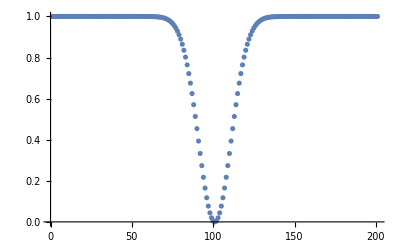

```mathematica
ListPlot[Table[S0[t,10,1,1,0,0,0.25,0,0,0.25]/.L->20^5(*,{x,-100000,100000}*),{t,0,20,0.1}],PlotRange->All,PlotLegends->Automatic]
```

```mathematica
1-(2+Tanh[(t-t0)/tau])^(-1/2)/.tau->1/10/.t0->15/.t->0//N
```

0.

```mathematica
S0[0,10,1,1,0,0,0.25,0,0,0.25]/.L->20^5//N
```

1.

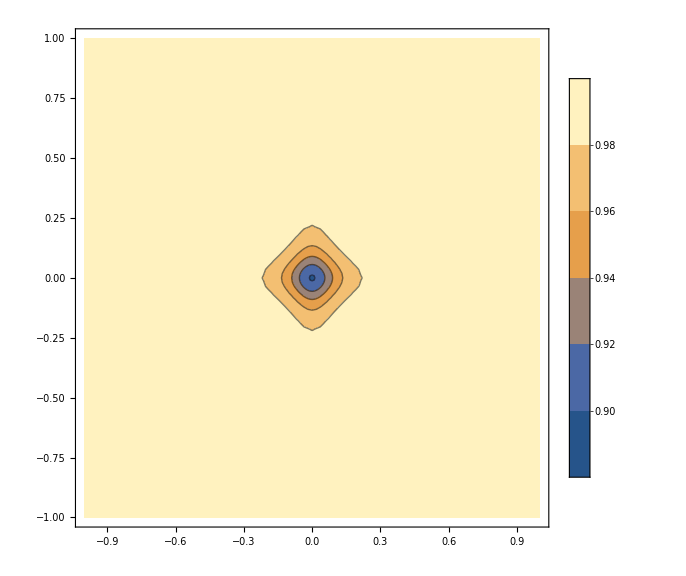

```mathematica
t0test=10;
tautest=10;
Atest=1;
sigmaxtest= 10^-1;
sigmaytest=10^-1;
x0test=0;
y0test=0;

ContourPlot[S0LC[0,t0test,tautest,Atest,x,x0test,sigmaxtest,y,y0test,sigmaytest]/.L->2,{x,-1,1},{y,-1,1},PlotRange->All,PlotLegends->Automatic,ImageSize->Large]
```

```mathematica
rules={A->GS[Amp],L->GS[L],x0->GS[x0],y0->GS[y0],Lsigmax->GS[Lsigmax],Lsigmay->GS[Lsigmay],t0->GS[t0],tau->GS[tau]}
```

{A→GS[Amp],L→GS[L],x0→GS[x0],y0→GS[y0],Lsigmax→GS[Lsigmax],Lsigmay→GS[Lsigmay],t0→GS[t0],tau→GS[tau]}

```mathematica
expr=S0LC[t,t0,tau,A,x,x0,Lsigmax,y,y0,Lsigmay(*,{x,1},{y,1}*)]//FullSimplify
```

1/(√(1+(A (1+Tanh[(t-t0)/tau]))/((1+(x-x0)^2/Lsigmax^2) (1+(y-y0)^2/Lsigmay^2))))

```mathematica
newExpr=expr/. rules//Simplify//FortranForm;
(*First,replace GS(...) safely*)expr1=StringReplace[ToString[newExpr],"GS("~~(param:(LetterCharacter|DigitCharacter)..)~~")":>"GS."<>param];
(*Then,process exponentiation and other fixes separately*)
expr2=StringReplace[expr1,{"E**"->"MathConstants.e^"}];
expr3=StringReplace[expr2,{"**"->"^"}];
expr4=StringReplace[expr3,{"**"->"^",(*Fix power notation after GS replacement*)"e"~~(x:DigitCharacter..):>"e"<>x,(*Fix scientific notation*)x:(DigitCharacter..)~~"."~~(y:Except[DigitCharacter]..):>x<>y,(*Remove unnecessary dots*)"Pi"->"pi",(*Mathematica uses'Pi',Julia uses'pi'*)"Tanh"->"tanh"}];
```

```mathematica
expr3//Print
```

1/Sqrt(1 + (GS.Amp*(1 + Tanh((t - GS.t0)/GS.tau)))/((1 + (x - GS.x0)^2/GS.Lsigmax^2)*(1 + (y - GS.y0)^2/GS.Lsigmay^2)))

```mathematica
SetOptions[$Output,PageWidth->Infinity];

(*Define the function Sz*)
Sz[t_,x_,y_]:=S0LC[t,t0,tau,A,x,0,Lsigmax,y,0,Lsigmay]; (*Replace'expr' with your actual function*)

(*Compute derivatives*)
Szx[t_,x_,y_]=D[Sz[t,x,y],x];
Szxx[t_,x_,y_]=D[Szx[t,x,y],x];
Szxxx[t_,x_,y_]=D[Szxx[t,x,y],x];
Szxxxx[t_,x_,y_]=D[Szxxx[t,x,y],x];

Szy[t_,x_,y_]=D[Sz[t,x,y],y];
Szxy[t_,x_,y_]=D[Szx[t,x,y],y];
Szxxy[t_,x_,y_]=D[Szxx[t,x,y],y];
Szxyy[t_,x_,y_]=D[Szxy[t,x,y],y];
Szxxyy[t_,x_,y_]=D[Szxxy[t,x,y],y];

Szyy[t_,x_,y_]=D[Szy[t,x,y],y];
Szyyy[t_,x_,y_]=D[Szyy[t,x,y],y];
Szyyyy[t_,x_,y_]=D[Szyyy[t,x,y],y];

Szt[t_,x_,y_]=D[Sz[t,x,y],t];
Sztt[t_,x_,y_]=D[Szt[t,x,y],t];
Sztx[t_,x_,y_]=D[Szt[t,x,y],x];
Szty[t_,x_,y_]=D[Szt[t,x,y],y];
Sztxx[t_,x_,y_]=D[Sztx[t,x,y],x];
Sztyy[t_,x_,y_]=D[Szty[t,x,y],y];
Sztxy[t_,x_,y_]=D[Sztx[t,x,y],y];


(*Function to process expressions*)
processExpression[expr_]:=Module[{newExpr,expr1,expr2,expr3,expr4},newExpr=expr/. rules//Simplify//FortranForm;
expr1=StringReplace[ToString[newExpr],"GS("~~(param:(LetterCharacter|DigitCharacter)..)~~")":>"GS."<>param];
expr2=StringReplace[expr1,{"E**"->"MathConstants.e^"}];
expr3=StringReplace[expr2,{"**"->"^"}];
expr4=StringReplace[expr3,{"Pi"->"pi"}];
expr5=StringReplace[expr4,{"**"->"^","e"~~(x:DigitCharacter..):>"e"<>x,x:(DigitCharacter..)~~"."~~(y:Except[DigitCharacter]..):>x<>y,"Pi"->"pi","Tanh"->"tanh","Sech"->"sech","Sqrt"->"sqrt","Sinh"->"sinh","Cosh"->"cosh"}];
expr5];
SourceType="LC";
(*Process all expressions*)
expressions={"Sz(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sz[t,x,y]],"Sz_x(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szx[t,x,y]],"Sz_xx(t, x, y, GS ::"<>SourceType<>") ="<>processExpression[Szxx[t,x,y]],"Sz_xxx(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxxx[t,x,y]],"Sz_xxxx(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxxxx[t,x,y]],"Sz_y(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szy[t,x,y]],"Sz_xy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxy[t,x,y]],"Sz_xxy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxxy[t,x,y]],"Sz_xyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxyy[t,x,y]],"Sz_xxyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxxyy[t,x,y]],"Sz_yy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szyy[t,x,y]],"Sz_yyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szyyy[t,x,y]],"Sz_yyyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szyyyy[t,x,y]],"Sz_t(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szt[t,x,y]],"Sz_tt(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztt[t,x,y]],"Sz_tx(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztx[t,x,y]],"Sz_ty(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szty[t,x,y]],"Sz_txx(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztxx[t,x,y]],"Sz_tyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztyy[t,x,y]],"Sz_txy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztxy[t,x,y]]};

(*Export to file*)
Export["/home/giulio/University/PhD/translated_expressions.txt",expressions,"Text"];
```

```mathematica
expressions[[6]]
```

Sz_y(t, x, y, GS ::LC) = (y*GS.Amp*(1 + tanh((t - GS.t0)/GS.tau)))/((1 + x^2/GS.Lsigmax^2)*(y^2/GS.Lsigmay + GS.Lsigmay)^2*(1 + (GS.Amp*(1 + tanh((t - GS.t0)/GS.tau)))/((1 + x^2/GS.Lsigmax^2)*(1 + y^2/GS.Lsigmay^2)))^1.5)

```mathematica
Sz[t,x,y]
```

1/(√(1+(A ⅇ^(-((2 π x)/L-x0)^2/(2 sigmax^2)-((2 π y)/L-y0)^2/(2 sigmay^2)) (1+Tanh[(t-t0)/tau]))/(4 π^2 sigmax^2 sigmay^2)))

```mathematica
D[S0[t,t0,tau,A,x,x0,sigmax,y,y0,sigmay],y]
```

(A ⅇ^(-((2 π x)/L-x0)^2/(2 sigmax^2)-((2 π y)/L-y0)^2/(2 sigmay^2)) ((2 π y)/L-y0) (1+Tanh[(t-t0)/tau]))/(4 L π sigmax^2 sigmay^4 (1+(A ⅇ^(-((2 π x)/L-x0)^2/(2 sigmax^2)-((2 π y)/L-y0)^2/(2 sigmay^2)) (1+Tanh[(t-t0)/tau]))/(4 π^2 sigmax^2 sigmay^2))^(3/2))

#### gtt Tanh Source

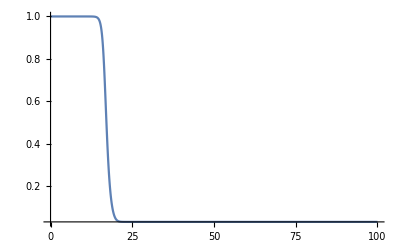

```mathematica
Plot[(1-A(1/2(1+Tanh[t-t0])))^(-1/2)/.A->-1000/.t0->20,{t,0,100},PlotRange->All]
```

```mathematica
1/150 1/((sigmax )^2 2Pi)/.sigmax->1/64//N
```

4.34599

```mathematica
S0[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_]:=(1-1/2(1+Tanh[(t-t0)/tau])A  (*1/((sigmax )^2 2Pi)*)Exp[(-( x -x0)^2)/(2 (L sigmax )^2)](*1/((sigmay )^2 2Pi)*)Exp[(-(y -y0)^2)/(2 (L sigmay )^2)])^(-1/2);
```

```mathematica
S0tilt[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_,phi_]:=1-1/2 (1+Tanh[(t-t0)/tau])*A*Exp[-1/2*((((x-x0) Cos[phi]+(y-y0) Sin[phi])^2)/(L sigmax)^2+((-(x-x0) Sin[phi]+(y-y0) Cos[phi])^2)/(L sigmay)^2)]//FullSimplify;
```

```mathematica
ListPlot[{Table[{t,S0[t,5000,300,0.8,0,0,0.25,0,0,0.25]/.L->500}(*,{x,-100000,100000}*),{t,0,10000}],Table[{t,S0[t,5000,2000,0.8,0,0,0.25,0,0,0.25]/.L->500}(*,{x,-100000,100000}*),{t,0,10000}],Table[{t,S0[t,5000,2000,0.5,0,0,0.25,0,0,0.25]/.L->500}(*,{x,-100000,100000}*),{t,0,15000}]},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
1/20000//N
```

0.00005

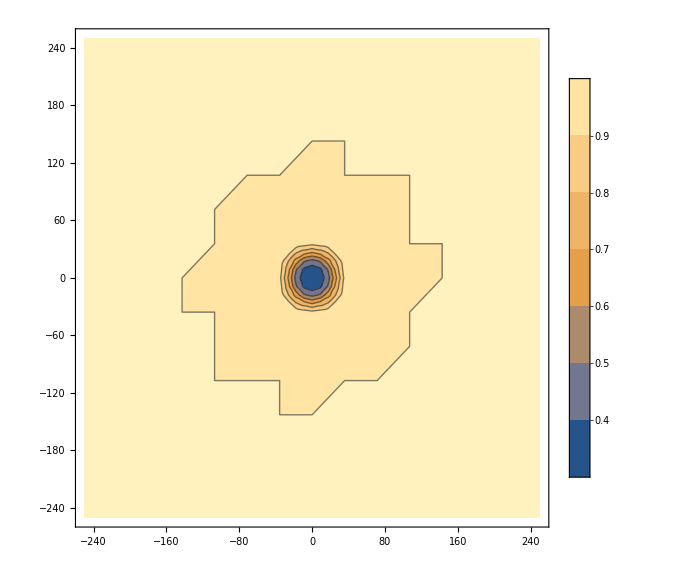

```mathematica
t0test=5000;
tautest=2000;
Atest=-0.8;
sigmaxtest= 1/20000 500;
sigmaytest=1/20000 500;
x0test=0;
y0test=0;

ContourPlot[{S0[10000,t0test,tautest,-10,x,x0test,sigmaxtest,y,y0test,sigmaytest]/.L->500},{x,-250,250},{y,-250,250},PlotRange->All,PlotLegends->Automatic,ImageSize->Large,AspectRatio->1/1]
(*ContourPlot[{S0[10000,t0test,tautest,Atest,x,x0test,sigmaxtest,y,y0test,sigmaytest]^-2/.L->1},{x,-750,750},{y,-250,250},PlotRange->All,PlotLegends->Automatic,ImageSize->Large,AspectRatio->1/3]*)
```

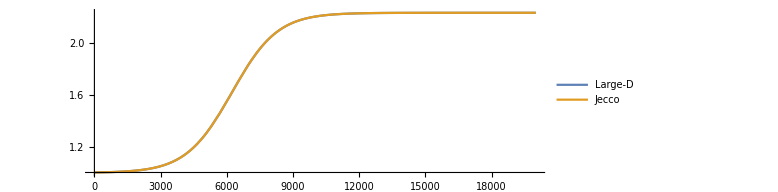

```mathematica
Plot[{D[S0[tt,5000,tautest,0.8,0,x0test,1/10 500,0,y0test,1/10 500]/.L->500/.x->0,{tt,0}]/.tt->{t},D[S0[tt,t0test,tautest,0.8,0,x0test,sigmaxtest,0,y0test,sigmaytest]/.L->500/.x->0,{tt,0}]/.tt->{t}},{t,0,20000},PlotRange->All,PlotLegends->{"Large-D","Jecco"},ImageSize->Large,AspectRatio->1/3]
```

```mathematica
rules={A->GS[Amp],L->GS[L],Lx->GS[Lx],Ly->GS[Ly],x0->GS[x0],y0->GS[y0],sigmax->GS[sigmax],sigmay->GS[sigmay],t0->GS[t0],tau->GS[tau],phi->GS[phi]}
```

{A→GS[Amp],L→GS[L],Lx→GS[Lx],Ly→GS[Ly],x0→GS[x0],y0→GS[y0],sigmax→GS[sigmax],sigmay→GS[sigmay],t0→GS[t0],tau→GS[tau],phi→GS[phi]}

```mathematica
expr=S0[t,t0,tau,A,x,x0,sigmax,y,y0,sigmay]//FullSimplify;//AbsoluteTiming
```

{0.000602,Null}

```mathematica
expr
```

1/(√(1-1/2 A ⅇ^(-((x-x0)^2/sigmax^2+(y-y0)^2/sigmay^2)/(2 L^2)) (1+Tanh[(t-t0)/tau])))

```mathematica
newExpr=expr/. rules//Simplify//FortranForm;
(*First,replace GS(...) safely*)expr1=StringReplace[ToString[newExpr],"GS("~~(param:(LetterCharacter|DigitCharacter)..)~~")":>"GS."<>param];
(*Then,process exponentiation and other fixes separately*)
expr2=StringReplace[expr1,{"E**"->"MathConstants.e^"}];
expr3=StringReplace[expr2,{"**"->"^"}];
expr4=StringReplace[expr3,{"**"->"^",(*Fix power notation after GS replacement*)"e"~~(x:DigitCharacter..):>"e"<>x,(*Fix scientific notation*)x:(DigitCharacter..)~~"."~~(y:Except[DigitCharacter]..):>x<>y,(*Remove unnecessary dots*)"Pi"->"pi",(*Mathematica uses'Pi',Julia uses'pi'*)"Tanh"->"tanh","Cos"->"cos","Sin"->"sin"}];
```

```mathematica
expr3//Print
```

1 - (GS.Amp*(1 + Tanh((t - GS.t0)/GS.tau)))/(2.*MathConstants.e^(((x - GS.x0)^2/GS.sigmax^2 + (y - GS.y0)^2/GS.sigmay^2)/(2.*L^2)))

```mathematica
SetOptions[$Output,PageWidth->Infinity];

(*Define the function Sz*)
Sz[t_,x_,y_]:=S0[t,t0,tau,A,x,x0,sigmax,y,y0,sigmay]; (*Replace'expr' with the actual function*)

(*Compute derivatives*)
Szx[t_,x_,y_]=D[Sz[t,x,y],x];
Szxx[t_,x_,y_]=D[Szx[t,x,y],x];
Szxxx[t_,x_,y_]=D[Szxx[t,x,y],x];
Szxxxx[t_,x_,y_]=D[Szxxx[t,x,y],x];

Szy[t_,x_,y_]=D[Sz[t,x,y],y];
Szxy[t_,x_,y_]=D[Szx[t,x,y],y];
Szxxy[t_,x_,y_]=D[Szxx[t,x,y],y];
Szxyy[t_,x_,y_]=D[Szxy[t,x,y],y];
Szxxyy[t_,x_,y_]=D[Szxxy[t,x,y],y];

Szyy[t_,x_,y_]=D[Szy[t,x,y],y];
Szyyy[t_,x_,y_]=D[Szyy[t,x,y],y];
Szyyyy[t_,x_,y_]=D[Szyyy[t,x,y],y];

Szt[t_,x_,y_]=D[Sz[t,x,y],t];
Sztt[t_,x_,y_]=D[Szt[t,x,y],t];
Sztx[t_,x_,y_]=D[Szt[t,x,y],x];
Szty[t_,x_,y_]=D[Szt[t,x,y],y];
Sztxx[t_,x_,y_]=D[Sztx[t,x,y],x];
Sztyy[t_,x_,y_]=D[Szty[t,x,y],y];
Sztxy[t_,x_,y_]=D[Sztx[t,x,y],y];


(*Function to process expressions*)
processExpression[expr_]:=Module[{newExpr,expr1,expr2,expr3,expr4},newExpr=expr/. rules//Simplify//FortranForm;
expr1=StringReplace[ToString[newExpr],"GS("~~(param:(LetterCharacter|DigitCharacter)..)~~")":>"GS."<>param];
expr2=StringReplace[expr1,{"E**"->"exp"}];
expr3=StringReplace[expr2,{"**"->"^"}];
expr4=StringReplace[expr3,{"Pi"->"pi"}];
expr5=StringReplace[expr4,{"**"->"^","e"~~(x:DigitCharacter..):>"e"<>x,x:(DigitCharacter..)~~"."~~(y:Except[DigitCharacter]..):>x<>y,"Pi"->"pi","Tanh"->"tanh","Sech"->"sech","Sqrt"->"sqrt","Sinh"->"sinh","Cosh"->"cosh","Cos"->"cos","Sin"->"sin"}];
expr5];
SourceType="Gaussiangtt";
(*Process all expressions*)
expressions={"Sz(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sz[t,x,y]],"Sz_x(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szx[t,x,y]],"Sz_xx(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxx[t,x,y]],"Sz_xxx(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxxx[t,x,y]],"Sz_xxxx(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxxxx[t,x,y]],"Sz_y(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szy[t,x,y]],"Sz_xy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxy[t,x,y]],"Sz_xxy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxxy[t,x,y]],"Sz_xyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxyy[t,x,y]],"Sz_xxyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szxxyy[t,x,y]],"Sz_yy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szyy[t,x,y]],"Sz_yyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szyyy[t,x,y]],"Sz_yyyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szyyyy[t,x,y]],"Sz_t(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szt[t,x,y]],"Sz_tt(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztt[t,x,y]],"Sz_tx(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztx[t,x,y]],"Sz_ty(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Szty[t,x,y]],"Sz_txx(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztxx[t,x,y]],"Sz_tyy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztyy[t,x,y]],"Sz_txy(t, x, y, GS ::"<>SourceType<>") = "<>processExpression[Sztxy[t,x,y]]};

(*Export to file*)
Export["/home/giulio/University/PhD/translated_expressions.txt",expressions,"Text"];
```

```mathematica
expressions[[6]]
```

Sz_y(t, x, y, GS ::Gaussiangtt) = Derivative(0,0,0,0,0,0,0,1,0,0,0)(S0)(t,GS.t0,GS.tau,GS.Amp,x,GS.x0,GS.sigmax,y,GS.y0,GS.sigmay,GS.phi)

```mathematica
Sz[t,x,y]
```

1-1/2 A ⅇ^(-(x-x0)^2/(2 L^2 sigmax^2)-(y-y0)^2/(2 L^2 sigmay^2)) (1+Tanh[(t-t0)/tau])

```mathematica
D[S0[t,t0,tau,A,x,x0,sigmax,y,y0,sigmay],y]
```

(A ⅇ^(-(x-x0)^2/(2 L^2 sigmax^2)-(y-y0)^2/(2 L^2 sigmay^2)) (y-y0) (1+Tanh[(t-t0)/tau]))/(2 L^2 sigmay^2)

#### Homogeneous Initil data

```mathematica
L=1500;
M=5;
kRadius=10;
kx=Table[Random[]-0.5,{i,1,M}];
ky=Table[Random[]-0.5,{i,1,M}];
ϕ=2 Pi Table[Random[],{i,1,M}];
kVectors=kRadius Map[Normalize,Transpose[{kx,ky}],{1}];
kVectors
```

{{7.33022,-6.80205},{-8.2211,-5.69329},{5.05667,-8.62729},{6.12455,-7.90505},{9.93904,1.10248}}

```mathematica
c=Table["c"<>ToString[i],{i,1,M}];
F[x_,y_,LL_]:=Sum[(*c[[i]]*)Cos[2 Pi/LL kVectors[[i]].{x,y}+ϕ[[i]]],{i,1,M}]//FullSimplify
```

```mathematica
Table["c"<>ToString[i]->1,{i,1,M}]
```

{c1→1,c2→1,c3→1,c4→1,c5→1}

```mathematica
(*F[x,y,L]*)(*/.Table["c"<>ToString[i]->1,{i,1,M}]*)
```

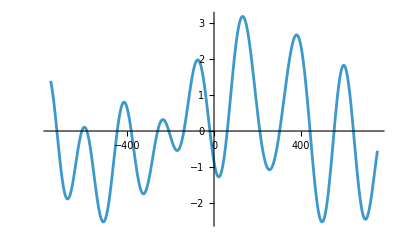

```mathematica
Plot[F[0,y,L],{y,-L/2,L/2}]
```

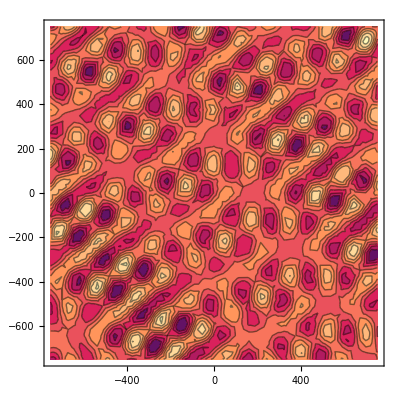

```mathematica
ContourPlot[F[x,y,L],{x,-L/2,L/2},{y,-L/2,L/2}]
```

```mathematica
7000/0.869/24//N
```

335.635

## Working Desk

```mathematica
1.1/36//N
```

0.0305556

```mathematica
1/25//N
```

0.04

```mathematica
test=Import["/home/giulio/University/PhD/Simulations/NBB_moving_gaussian_L500_0d1iu12_1u036_x150_u0d1_tzero20_tau1_A0d006_rec1/constrained_00060500.h5"];
```

Import::nffil: File «139» not found during «6».